# Normalized Additional Velocity (NAV)

By Davi Rodrigues & Alejandro Hernandez-Arboleda
September, 2022

The method is described in detail in the paper:
  Normalized Additional Velocity: a fast sample analysis for dark matter or modified gravity models
  A.Hernandez-Arboleda, D.C. Rodrigues, A.Wojnar

## Prelude

```mathematica
saveAllPlots = False; (*Change this to True to save ALL the plots that are generated in THIS notebook. It does not include NAVobservational plots. Saves for specific models are in their respective sections.*)
saveNAVobservationalPlots = False;
saveNAVobservationalTables = False;

pathBaseDirectory = NotebookDirectory[];
pathOutputDirectory = FileNameJoin[{pathBaseDirectory, "Output"}];
pathAuxDirectory = FileNameJoin[{pathBaseDirectory, "AuxiliaryData"}];

datasetExpVdiskNoBulge = Import[FileNameJoin[{pathOutputDirectory, "datasetExpVdiskNoBulge.m"}]]; (*Loads the exponential approximations for the stellar disk as a DataSet*)
datasetExpVgasNoBulge = Import[FileNameJoin[{pathOutputDirectory, "datasetExpVgasNoBulge.m"}]]; (*The same as above, but for the gas.*)

SetDirectory @ pathBaseDirectory;

Needs @ "NAVbaseCode`";
Get @ "NAVoptions.wl";
Get @ "NAVobservational.wl";
Get @ "NAVauxiliaryFunctions.wl";
Get["MDC14aux.mx", Path -> pathAuxDirectory] // Quiet; (*If something goes wrong, this file will be generated*)

SetDirectory @ pathOutputDirectory;

savePreviousPlot[fileName_] := If[saveThisPlot || saveAllPlots, 
  Echo @ Export[ToString @ fileName, %]; saveThisPlot = False
];
```

Starting NAVobservational...

"list2RARRot"  0.021096

"distRAR"  17.6173

"plotBlueRAR"  19.8434

"plotSigmaRegions"  0.213536

## Brief ΔV^2 analysis

{0.937222,-3.12634}

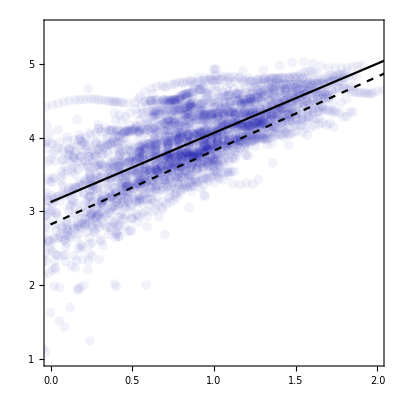

```mathematica
saveThisPlot = False;

Clear[b, loga, model, logR];
model = b logR - loga;
{b , loga} = {b, loga} /. FindFit[Re[{Log10[#1] , Log10[#2]} & @@@ Flatten[gdR[{Rad, Vmiss2}],1]],  model , {b , loga} , logR]

Show[
  plotBlueZero[
    {Log10[#1], Log10[#2]} & @@@ Flatten[gdR[{Rad, Vmiss2}], 1], 
    PlotRange-> {{0,2}, {1,5.5}}
  ],
  Plot[{Log10[10^logR/0.0015], model}, {logR, 0, 3}, PlotStyle->{{Black, Dashed}, Black}]
]

savePreviousPlot["DeltaV2analysis.pdf"];
```

Dashed line: McGaugh ApJ 2007. Black line: best fit from the SPARC data.

## TYPE 1 MODELS:

## 0. Polynomial approximation

Models considered here :
    r^a -- for monotonic curves
  2 r^a - r^b -- for non - monotonic curves

  Both cases satisfy δV (0) = 0 and δV (1) = 1.
  
  The fits are done considering data between 0.2 < rn < 0.9 .

{0.415394}

{0.376723,1.92178}

{2.24473}

{0.576874,1.65699}

{0.868438}

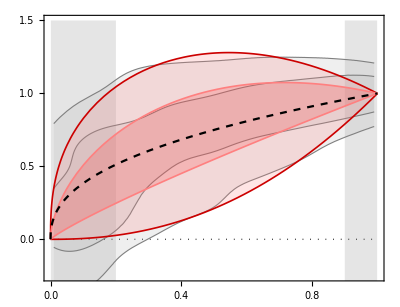

```mathematica
saveThisPlot = False;

Clear[ac];
list2restrictedRARRot = Select[list2RARRot, 0.2 <  #[[1]] < 0.9 &] ;
{ac} ={ac} /. FindFit[list2restrictedRARRot,  r^ac , ac , r]

Clear[a, b, c, d, e, f, g, h];

list = Table[{r, list1InterpCurvesRAR[[4]][r]}, {r,0.2, 0.9, 0.05}];
{c, d} = {c , d}/. FindFit[list, {2 r^c -  r^d},  {c, d}, r]

list = Table[{r, list1InterpCurvesRAR[[3]][r]}, {r,0.2, 0.9, 0.05}];
{b} = {b}/. FindFit[list, r^b,  {b}, r]

list = Table[{r, list1InterpCurvesRAR[[2]][r]}, {r,0.2, 0.9, 0.05}];
{e, f} = {e, f}/. FindFit[list, {2 r^e -  r^f},  {e, f}, r]

list = Table[{r, list1InterpCurvesRAR[[1]][r]}, {r,0.2, 0.9, 0.05}];
{g} = {g}/. FindFit[list, r^g ,  {g}, r]

plotPowerLawModel = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        2 rn^c - rn^d, 
        2 rn^e -  rn^f,  
        rn^b, 
        rn^g
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Red, 0.2], Thickness @ 0.003},
        {Lighter[Red, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Red, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Red, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ],
    Plot[rn^ac, {rn,0,1}, PlotStyle -> {Black, Dashed}]
  }
]

savePreviousPlot["plotPowerLawModel.pdf"];
```

### NAV efficiency

```mathematica
efficiencyNAV[#^g &, 2 #^e - #^f &, 1]
efficiencyNAV[#^b &, 2 #^c - #^d &, 2]
efficiencyNAVtotal[#^g &, 2 #^e - #^f &, #^b &, 2 #^c - #^d &]
```

{0.807192,0.901866,0.0946741}

{0.908244,0.945761,0.0375164}

{0.857718,0.923813,0.0660953}

## I. ArcTan models

## ArcTan

plotArctanGrayRed:

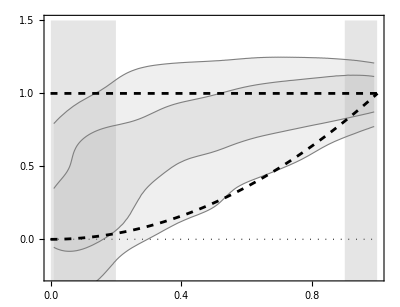

```mathematica
δVarctan[rn_, rtn_] = ArcTan[rn/rtn]^2/ArcTan[1/rtn]^2;

δVarctanLimit1[rn_] = Limit[δVarctan[rn, rtn], rtn -> ∞];
δVarctanLimit2[rn_] = Limit[δVarctan[rn, rtn], rtn -> 0];
  

plotArctanGrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        δVarctanLimit1[rn], 
        δVarctanLimit2[rn]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Thickness[0.005], Black, Dashed}}
    ]
  }
];

Echo["plotArctanGrayRed:"];
Print@plotArctanGrayRed;
```

Performing the optimization.

rtn 1σ bounds:   {0.0358811,0.373523}

rtn 2σ bounds:   {0.001,22553.4}

plotArctanGlobalBestFit:

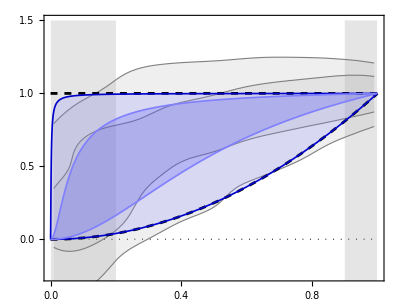

```mathematica
saveThisPlot = False;

(* DEFINITIONS *)

rnStart = 0.2;
rnEnd = 0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];

Clear[chi2Upper, chi2Lower];
chi2Upper[rtn_?NumberQ, nσ_] := NIntegrate[
  (upperBound[nσ][rn] - δVarctan[rn,rtn])^2, 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];

chi2Lower[rtn_?NumberQ, nσ_] := NIntegrate[
  (lowerBound[nσ][rn] - δVarctan[rn,rtn])^2, 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing"-> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];


(* EXECUTION *)

Echo["Performing the optimization."];

rtnUpper[2] = rtn /. NMinimize[{chi2Upper[rtn,2],rtn>0.001},{rtn,0,10}][[2]];
rtnUpper[1] = rtn /. NMinimize[{chi2Upper[rtn,1],rtn>0.001},{rtn,0,10}][[2]];
rtnLower[2] = rtn /. NMinimize[{chi2Lower[rtn,2],rtn>0.001},{rtn,0,10}][[2]];
rtnLower[1] = rtn /. NMinimize[{chi2Lower[rtn,1],rtn>0.001},{rtn,0,10}][[2]];

Echo[{rtnUpper[1], rtnLower[1]}, "rtn 1σ bounds: "];
Echo[{rtnUpper[2], rtnLower[2]}, "rtn 2σ bounds: "];

plotArctanGlobalBestFit = Show[
  {
    plotArctanGrayRed,
    Plot[
      {
        δVarctan[rn, rtnUpper @ 2],
        δVarctan[rn, rtnUpper @ 1],
        δVarctan[rn, rtnLower @ 2],
        δVarctan[rn, rtnLower @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotArctanGlobalBestFit:"];
Print@plotArctanGlobalBestFit;

savePreviousPlot["plotArctanGlobalBestFit.pdf"];
```

### NAV efficiency

```mathematica
efficiencyNAV[δVarctan[#, rtnLower@ 1] &, δVarctan[#, rtnUpper@ 1] &, 1]
efficiencyNAV[δVarctan[#, rtnLower@ 2] &, δVarctan[#, rtnUpper@ 2] &, 2]
(0.68%% + 0.27 %)/0.95
efficiencyNAVtotal[δVarctan[#, rtnLower@ 1] &, δVarctan[#, rtnUpper@ 1] &, δVarctan[#, rtnLower@ 2] &, δVarctan[#, rtnUpper@ 2] &]
```

{0.694453,0.764207,0.0697544}

{0.704059,0.708604,0.00454534}

{0.697183,0.748404,0.0512213}

{0.699256,0.736406,0.0371499}

### Comparison with individual fits

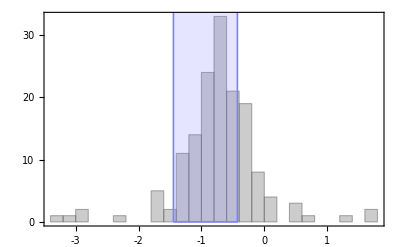

```mathematica
saveThisPlot = False;

resultsArctan = Get["../AuxiliaryData/arctan-GY-1-MAGMAtableResults.m"]; (*These results only inlcude the 153 RAR galaxies*)
headerArctan = First @ resultsArctan;
resultsArctanData = Drop[resultsArctan, 1];
colRt = First @ Flatten @ Position[headerArctan, "Rt"];
listRtn = resultsArctanData[[All, colRt]] / (rmax153 /@ Range @ 153);
rectangle = {
  EdgeForm[{Lighter[Blue, 0.5], Thickness @ 0.003}],
  Lighter[Blue, 0.5],
  Opacity @ 0.2,
  Rectangle[{Log10@rtnUpper @ 1, 0}, {Log10@rtnLower @ 1, 100}]
};

Histogram[
  Log10 @ listRtn, 
  {0.2}, 
  PlotRange -> All,
  Frame -> True, 
  Axes -> False, 
  Epilog -> {rectangle},
  histoOptions
]

savePreviousPlot["histogramArctan.pdf"];
```

```mathematica
listArctanChi2 = resultsArctanData[[All, colChi2]];
Echo[Median @ listArctanChi2, "Median: "];
Echo[Total @ listArctanChi2, "Total: "];
```

Median:   8.89515

Total:   7485.48

## ArcTanHalf

plotArctanHalfGrayRed:

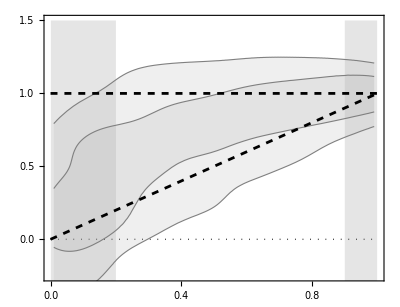

```mathematica
δVarctanHalf[rn_, rtn_] = ArcTan[rn/rtn]/ArcTan[1/rtn];

δVarctanHalfLimit1[rn_] = Limit[δVarctanHalf[rn, rtn], rtn -> ∞];
δVarctanHalfLimit2[rn_] = Simplify[Limit[δVarctanHalf[rn, rtn], rtn -> 0], rn > 0];
  

plotArctanHalfGrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        δVarctanHalfLimit1[rn], 
        δVarctanHalfLimit2[rn]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Thickness[0.005], Black, Dashed}}
    ]
  }
];

Echo["plotArctanHalfGrayRed:"];
Print@plotArctanHalfGrayRed;
```

Performing the optimization.

rtn 1σ bounds:   {0.0696424,1.24667}

rtn 2σ bounds:   {0.001,43285.4}

plotArctanHalfGlobalBestFit:

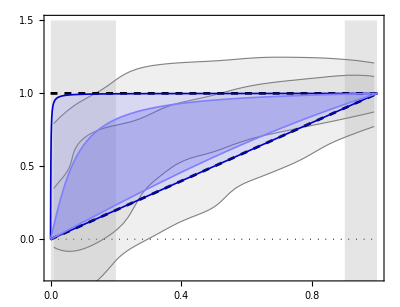

```mathematica
saveThisPlot = False;

(* DEFINITIONS *)

rnStart = 0.2;
rnEnd = 0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];

Clear[chi2Upper, chi2Lower];
chi2Upper[rtn_?NumberQ, nσ_] := NIntegrate[
  (upperBound[nσ][rn] - δVarctanHalf[rn,rtn])^2, 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];

chi2Lower[rtn_?NumberQ, nσ_] := NIntegrate[
  (lowerBound[nσ][rn] - δVarctanHalf[rn,rtn])^2, 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing"-> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];


(* EXECUTION *)

Echo["Performing the optimization."];

rtnUpper[2] = rtn /. NMinimize[{chi2Upper[rtn,2],rtn>0.001},{rtn,0,10}][[2]];
rtnUpper[1] = rtn /. NMinimize[{chi2Upper[rtn,1],rtn>0.001},{rtn,0,10}][[2]];
rtnLower[2] = rtn /. NMinimize[{chi2Lower[rtn,2],rtn>0.001},{rtn,0,10}][[2]];
rtnLower[1] = rtn /. NMinimize[{chi2Lower[rtn,1],rtn>0.001},{rtn,0,10}][[2]];

Echo[{rtnUpper[1], rtnLower[1]}, "rtn 1σ bounds: "];
Echo[{rtnUpper[2], rtnLower[2]}, "rtn 2σ bounds: "];

plotArctanHalfGlobalBestFit = Show[
  {
    plotArctanHalfGrayRed,
    Plot[
      {
        δVarctanHalf[rn, rtnUpper @ 2],
        δVarctanHalf[rn, rtnUpper @ 1],
        δVarctanHalf[rn, rtnLower @ 2],
        δVarctanHalf[rn, rtnLower @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotArctanHalfGlobalBestFit:"];
Print@plotArctanHalfGlobalBestFit;

savePreviousPlot["plotArctanHalfGlobalBestFit.pdf"];
```

### NAV efficiency

```mathematica
efficiencyNAV[δVarctanHalf[#, rtnLower@ 1] &, δVarctanHalf[#, rtnUpper@ 1] &, 1]
efficiencyNAV[δVarctanHalf[#, rtnLower@ 2] &, δVarctanHalf[#, rtnUpper@ 2] &, 2]
(0.68%% + 0.27 %)/0.95
efficiencyNAVtotal[δVarctanHalf[#, rtnLower@ 1] &, δVarctanHalf[#, rtnUpper@ 1] &, δVarctanHalf[#, rtnLower@ 2] &, δVarctanHalf[#, rtnUpper@ 2] &]
```

{0.709364,0.78197,0.0726068}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.489001,0.489001,0.}

{0.646734,0.698705,0.0519712}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.599182,0.635486,0.0363034}

The integration errors above are for the “areaModelOut”, which at 2σ is indeed null. Hence there is no mistake.

### Comparison with individual fits: Gaussian Y

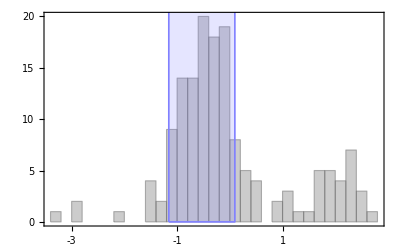

```mathematica
saveThisPlot = False;

resultsArctanHalf = Get["../AuxiliaryData/arctanHalf-GY-1-MAGMAtableResults.m"]; (*These results only inlcude the 153 RAR galaxies*)
headerArctanHalf = First @ resultsArctanHalf;
resultsArctanHalfData = Drop[resultsArctanHalf, 1];
colRt = First @ Flatten @ Position[headerArctanHalf, "Rt"];
listRtnHalf = resultsArctanHalfData[[All, colRt]] / (rmax153 /@ Range @ 153);
rectangle = {
  EdgeForm[{Lighter[Blue, 0.5], Thickness @ 0.003}],
  Lighter[Blue, 0.5],
  Opacity @ 0.2,
  Rectangle[{Log10@rtnUpper @ 1, 0}, {Log10@rtnLower @ 1, 100}]
};

Histogram[
  Log10 @ listRtnHalf, 
  {0.2}, 
  PlotRange -> All,
  Frame -> True, 
  Axes -> False, 
  Epilog -> {rectangle},
  histoOptions
]

savePreviousPlot["histogramArctanHalf.pdf"];
```

As expected, there are several cases with rtn > 10, and even many cases with rtn > 100. The latter reached the maximum

```mathematica
listArctanHalfChi2 = resultsArctanHalfData[[All, colChi2]];
Echo[Median @ listArctanHalfChi2, "Median: "];
Echo[Total @ listArctanHalfChi2, "Total: "];
```

Median:   18.9855

Total:   9867.32

### Comparison with individual fits: Fixed Y

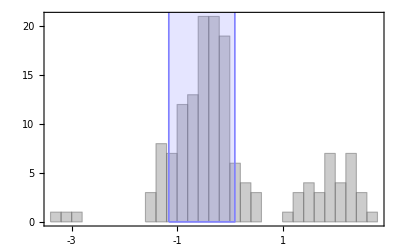

```mathematica
saveThisPlot = False;

resultsArctanHalfFixed = Get["../AuxiliaryData/arctanHalf-Fixed-05-06-MAGMAtableResults.m"]; (*These results only inlcude the 153 RAR galaxies*)
headerArctanHalfFixed = First @ resultsArctanHalfFixed;
resultsArctanHalfDataFixed = Drop[resultsArctanHalfFixed, 1];
colRt = First @ Flatten @ Position[headerArctanHalfFixed, "Rt"];
listRtnHalfFixed = resultsArctanHalfDataFixed[[All, colRt]] / (rmax153 /@ Range @ 153);
rectangle = {
  EdgeForm[{Lighter[Blue, 0.5], Thickness @ 0.003}],
  Lighter[Blue, 0.5],
  Opacity @ 0.2,
  Rectangle[{Log10@rtnUpper @ 1, 0}, {Log10@rtnLower @ 1, 100}]
};

Histogram[
  Log10 @ listRtnHalfFixed, 
  {0.2}, 
  PlotRange -> All,
  Frame -> True, 
  Axes -> False, 
  Epilog -> {rectangle},
  histoOptions
]

savePreviousPlot["histogramArctanHalfFixed.pdf"];
```

As expected, there are several cases with rtn > 10, and even many cases with rtn > 100. The latter reached the maximum

```mathematica
listArctanHalfChi2Fixed = resultsArctanHalfDataFixed[[All, colChi2]];
Echo[Median @ listArctanHalfChi2Fixed, "Median: "];
Echo[Total @ listArctanHalfChi2Fixed, "Total: "];
```

Median:   23.4476

Total:   21086.5

## II. Burkert

plotBurkertGrayRed:

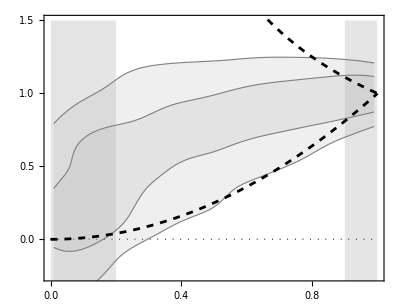

```mathematica
ρbrkt[rn_, rcn_, ρ0_] = ρ0/((1+rn/rcn)(1+rn^2/rcn^2));
Mbrkt[rn_, rcn_, ρ0_] = 4 π Rmax^3 Integrate[ρbrkt[rnprime,rcn,ρ0] rnprime^2,{rnprime,0,rn}, Assumptions-> {rn>0, rcn>0}];

VVbrkt[rn_, rcn_, ρ0_, Rmax_] = (G / Rmax) * Mbrkt[rn, rcn, ρ0] / rn;

δVbrkt[rn_, rcn_] = FullSimplify[
  VVbrkt[rn, rcn, ρ0, Rmax] / VVbrkt[1, rcn, ρ0, Rmax],
  Assumptions -> {0 < rn < 1, 0 < rcn < 1, 0 < Rmax}
];

plotBurkertGrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        rn^2, (*These are the limiting curves for Burkert.*)
        1/rn
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Thickness[0.005], Black, Dashed}}
    ]
  }
];

Echo["plotBurkertGrayRed:"];
Print@plotBurkertGrayRed;
```

Performing the optimization.

rcn 1σ bounds:   {0.196103,0.58212}

rcn 2σ bounds:   {0.116784,34.9365}

plotBurkertGlobalBestFit:

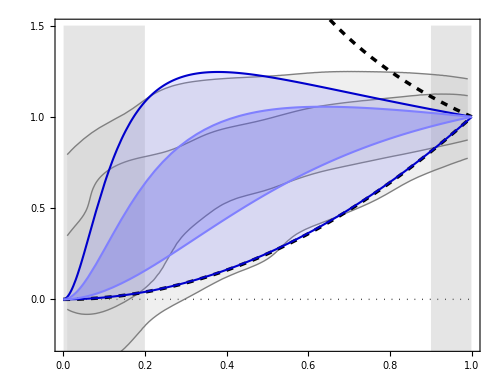

```mathematica
Clear[chi2Upper, chi2Lower];
chi2Upper[rcn_?NumberQ, nσ_]:= (*chi2Upper[rcn, nσ] =*) NIntegrate[
  (upperBound[nσ][rn] - δVbrkt[rn,rcn])^2, 
  {rn,rnStart,rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];

chi2Lower[rcn_?NumberQ, nσ_]:= chi2Lower[rcn, nσ] = NIntegrate[
  (lowerBound[nσ][rn]- δVbrkt[rn,rcn])^2, 
  {rn,rnStart,rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing"-> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];


(* SPECIFIC DEFINITIONS *)

rnStart = 0.2;
rnEnd=0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

rcnUpper[2] = rcn /. NMinimize[{chi2Upper[rcn,2],rcn>0},{rcn,0,10}][[2]];
rcnUpper[1] = rcn /. NMinimize[{chi2Upper[rcn,1],rcn>0},{rcn,0,10}][[2]];
rcnLower[2] = rcn /. NMinimize[{chi2Lower[rcn,2],rcn>0},{rcn,0,10}][[2]];
rcnLower[1] = rcn /. NMinimize[{chi2Lower[rcn,1],rcn>0},{rcn,0,10}][[2]];

Echo[{rcnUpper[1], rcnLower[1]}, "rcn 1σ bounds: "];
Echo[{rcnUpper[2], rcnLower[2]}, "rcn 2σ bounds: "];

plotBurkertGlobalBestFit = Show[
  {
    plotBurkertGrayRed,
    Plot[
      {
        δVbrkt[rn, rcnUpper @ 2],
        δVbrkt[rn, rcnUpper @ 1],
        δVbrkt[rn, rcnLower @ 2],
        δVbrkt[rn, rcnLower @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotBurkertGlobalBestFit:"];
Print@plotBurkertGlobalBestFit;

Export["plotBurkertGlobalBestFit.pdf", plotBurkertGlobalBestFit];
```

### NAV efficiency

```mathematica
efficiencyNAV[δVbrkt[#, rcnLower@ 1] &, δVbrkt[#, rcnUpper@ 1] &, 1]
efficiencyNAV[δVbrkt[#, rcnLower@ 2] &, δVbrkt[#, rcnUpper@ 2] &, 2]
(0.68%% + 0.27 %)/0.95
efficiencyNAVtotal[δVbrkt[#, rcnLower@ 1] &, δVbrkt[#, rcnUpper@ 1] &, δVbrkt[#, rcnLower@ 2] &, δVbrkt[#, rcnUpper@ 2] &]
```

{0.738335,0.833853,0.0955181}

{0.86247,0.878446,0.0159759}

{0.773616,0.846527,0.0729113}

{0.800403,0.85615,0.055747}

### Comparison with individual fits

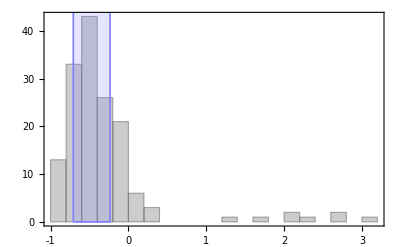

```mathematica
saveThisPlot = False;

resultsBurkert = Get["../AuxiliaryData/Burkert-GY-05-06-MAGMAtableResults.m"]; (*These results include all 175 galaxies*)
headerBurkert = First @ resultsBurkert;
resultsBurkertData = Drop[resultsBurkert, 1];
colRc = First @ Flatten @ Position[headerBurkert, "rc"];
listRcn = DeleteCases[resultsBurkertData[[All, colRc]] / (rmax /@ Range @ 175), _/Last[{}]] // Quiet;
rectangle = {
  EdgeForm[{Lighter[Blue, 0.5], Thickness @ 0.003}],
  Lighter[Blue, 0.5],
  Opacity @ 0.2,
  Rectangle[{Log10@rcnUpper @ 1, 0}, {Log10@rcnLower @ 1, 100}]
};

Histogram[
  Log10 @ listRcn, 
  {0.2}, 
  PlotRange -> {All, All}, (*There are a few galaxies beyond 1*)
  Frame -> True, 
  Axes -> False, 
  Epilog -> {rectangle},
  histoOptions
]

savePreviousPlot["histogramBurkert.pdf"];
```

As expected, there are not many cases of rcn too small or too large.

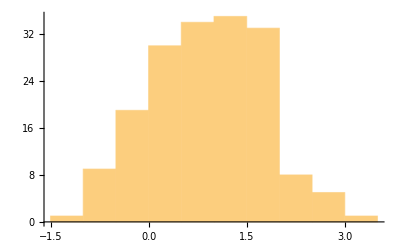

Median:   8.1357

Total:   8238.22

```mathematica
listBurkertChi2 = resultsBurkertData[[All, colChi2]];
Histogram[Log10@listBurkertChi2, PlotRange->All]
Echo[Median @ listBurkertChi2, "Median: "];
Echo[Total @ listBurkertChi2, "Total: "];
```

## III. NFW

### III.1 NFW definition and limiting cases

Using rsn for the normalized rs: rs/Rmax and rn for the normalized radius: r/Rmax, the mass and the additional normalized velocity can be them easily computed:

```mathematica
ρnfw[rn_, rsn_, ρs_] = ρs/(rn/rsn(1+rn/rsn)^2);
Mnfw[rn_, rsn_, ρs_] = 4 π Rmax^3 Integrate[ρnfw[rnprime, rsn, ρs] rnprime^2, {rnprime, 0, rn}, Assumptions-> {rn>0, rsn>0}];

VVnfw[rn_, rsn_, ρs_, Rmax_] = (G / Rmax) * Mnfw[rn, rsn, ρs] / rn;

δVnfw[rn_, rsn_] = FullSimplify[
  VVnfw[rn, rsn, ρs, Rmax] / VVnfw[1, rsn, ρs, Rmax],
  Assumptions -> {0 < rn < 1, 0 < Rmax}
]

δVnfwLargeRsn[rn_] = Limit[δVnfw[rn, rsn], rsn -> ∞]
δVnfwSmallRsn[rn_] = Limit[δVnfw[rn, rsn], rsn -> 0]
```

-(-rn/(rn+rsn)-Log[rsn]+Log[rn+rsn])/(rn (1/(1+rsn)+Log[rsn]-Log[1+rsn]))

rn

1/rn

plotNFWGrayRed:

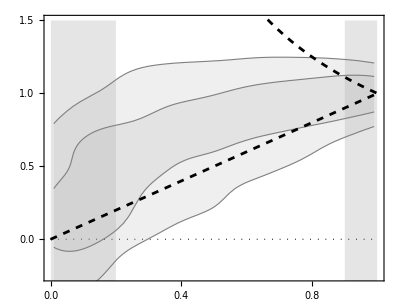

```mathematica
plotNFWGrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        δVnfwLargeRsn[rn], 
        δVnfwSmallRsn[rn]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Thickness[0.005], Black, Dashed}}
    ]
  }
];

Echo["plotNFWGrayRed:"];
Print@plotNFWGrayRed;
```

Performing the optimization.

rsn 1σ bounds:   {0.327763,4.91399}

rsn 2σ bounds:   {0.150412,24790.}

plotNFWGlobalBestFit:

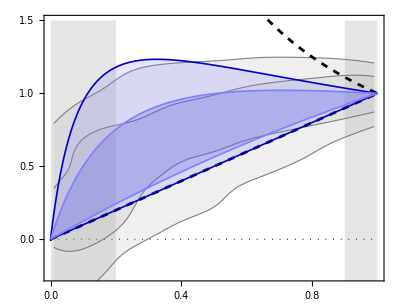

plotNFWGlobalBestFit.pdf

```mathematica
saveThisPlot = True;

Clear[chi2Upper, chi2Lower];
chi2Upper[rsn_?NumberQ, nσ_]:= (*chi2Upper[rcn, nσ] =*) NIntegrate[
  (upperBound[nσ][rn] - δVnfw[rn,rsn])^2, 
  {rn,rnStart,rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];

chi2Lower[rsn_?NumberQ, nσ_]:= chi2Lower[rsn, nσ] = NIntegrate[
  (lowerBound[nσ][rn]- δVnfw[rn,rsn])^2, 
  {rn,rnStart,rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing"-> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];


(* SPECIFIC DEFINITIONS *)

rnStart = 0.2;
rnEnd=0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

rsnUpper[2] = rsn /. NMinimize[{chi2Upper[rsn,2], rsn > 0}, {rsn, 0, 1}][[2]];
rsnUpper[1] = rsn /. NMinimize[{chi2Upper[rsn,1], rsn > 0}, {rsn, 0, 1}][[2]];
rsnLower[2] = rsn /. NMinimize[{chi2Lower[rsn,2], rsn > 0}, {rsn, 10, 10000}][[2]];
rsnLower[1] = rsn /. NMinimize[{chi2Lower[rsn,1], rsn > 0}, {rsn, 10, 10000}][[2]];

Echo[{rsnUpper[1], rsnLower[1]}, "rsn 1σ bounds: "];
Echo[{rsnUpper[2], rsnLower[2]}, "rsn 2σ bounds: "];

plotNFWGlobalBestFit = Show[
  {
    plotNFWGrayRed,
    Plot[
      {
        δVnfw[rn, rsnUpper @ 2],
        δVnfw[rn, rsnUpper @ 1],
        δVnfw[rn, rsnLower @ 2],
        δVnfw[rn, rsnLower @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotNFWGlobalBestFit:"];
plotNFWGlobalBestFit

savePreviousPlot["plotNFWGlobalBestFit.pdf"];
```

### NAV efficiency

```mathematica
efficiencyNAV[δVnfw[#, rsnLower@ 1] &, δVnfw[#, rsnUpper@ 1] &, 1]
efficiencyNAV[δVnfw[#, rsnLower@ 2] &, δVnfw[#, rsnUpper@ 2] &, 2]
(0.68%% + 0.27 %)/0.95
efficiencyNAVtotal[δVnfw[#, rsnLower@ 1] &, δVnfw[#, rsnUpper@ 1] &, δVnfw[#, rsnLower@ 2] &, δVnfw[#, rsnUpper@ 2] &]
```

{0.771351,0.843344,0.0719928}

{0.633047,0.648073,0.0150251}

{0.732044,0.787845,0.055802}

{0.702199,0.745708,0.0435089}

### Comparison with the rsn distribution found from the individual NFW fits

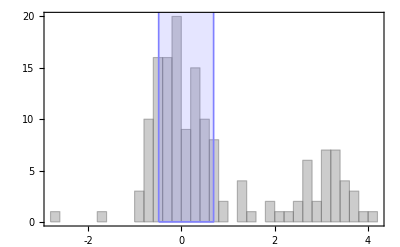

```mathematica
saveThisPlot = False;

resultsNFW = Get["../AuxiliaryData/NFW-GY-05-06-v2-MAGMAtableResults.m"]; (*These results include all 175 galaxies*)
headerNFW = First @ resultsNFW;
resultsNFWData = Drop[resultsNFW, 1];
colRs = First @ Flatten @ Position[headerNFW, "rS"];
resultsNFWDataRAR = Delete[resultsNFWData,  GalaxiesOutsideRAR];
listRsnRAR = resultsNFWDataRAR[[All, colRs]] / (rmax153 /@ Range @ 153);
rectangle = {
  EdgeForm[{Lighter[Blue, 0.5], Thickness @ 0.003}],
  Lighter[Blue, 0.5],
  Opacity @ 0.2,
  Rectangle[{Log10@rsnUpper @ 1, 0}, {Log10@rsnLower @ 1, 100}]
};

Histogram[
  Log10 @ listRsnRAR, 
  {0.2}, 
  PlotRange -> {All, All}, 
  Frame -> True, 
  Axes -> False, 
  Epilog -> {rectangle},
  histoOptions
]

savePreviousPlot["histogramNFW.pdf"];
```

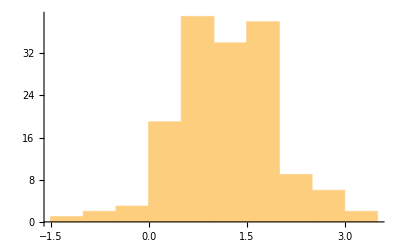

Median:   19.175

Total:   10058.6

```mathematica
listNFWChi2 = resultsNFWDataRAR[[All, colChi2]];
Histogram[Log10@listNFWChi2, PlotRange->All]
Echo[Median @ listNFWChi2, "Median: "];
Echo[Total @ listNFWChi2, "Total: "];
```

### Comparison with the rsn distribution found from the individual NFW fits: Fixed Case

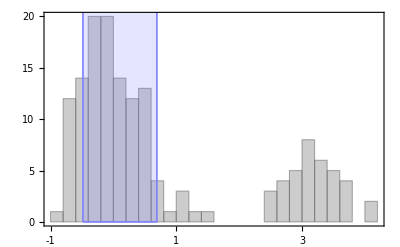

```mathematica
saveThisPlot = False;

resultsNFWfixed = Get["../AuxiliaryData/NFW-Fixed-05-06-v2-MAGMAtableResults.m"]; (*These results include all 175 galaxies*)
headerNFWfixed = First @ resultsNFWfixed;
resultsNFWDataFixed = Drop[resultsNFWfixed, 1];
colRsFixed = First @ Flatten @ Position[headerNFWfixed, "rS"];
resultsNFWDataRARfixed = Delete[resultsNFWDataFixed,  GalaxiesOutsideRAR];
listRsnRARfixed = resultsNFWDataRARfixed[[All, colRs]] / (rmax153 /@ Range @ 153);
rectangle = {
  EdgeForm[{Lighter[Blue, 0.5], Thickness @ 0.003}],
  Lighter[Blue, 0.5],
  Opacity @ 0.2,
  Rectangle[{Log10@rsnUpper @ 1, 0}, {Log10@rsnLower @ 1, 100}]
};

Histogram[
  Log10 @ listRsnRARfixed, 
  {0.2}, 
  PlotRange -> {All, All}, 
  Frame -> True, 
  Axes -> False, 
  Epilog -> {rectangle},
  histoOptions
]

savePreviousPlot["histogramNFWfixed.pdf"];
```

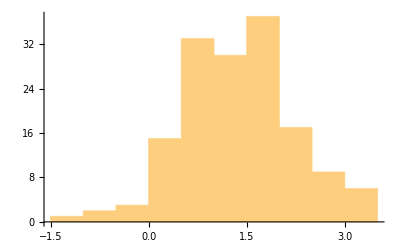

Median:   25.9323

Total:   22525.2

```mathematica
listNFWChi2Fixed = resultsNFWDataRARfixed[[All, colChi2]];
Histogram[Log10@listNFWChi2Fixed, PlotRange->All]
Echo[Median @ listNFWChi2Fixed, "Median: "];
Echo[Total @ listNFWChi2Fixed, "Total: "];
```

## IV. DC 14

## Introduction

```mathematica
Clear[X, ρ, α,γ,β]
α = 2.94 - Log10[(10^(X + 2.33))^-1.08 + (10^(X + 2.33))^2.29];
β = 4.23 + 1.34 X + 0.26 X^2;
γ = - 0.06 + Log10[(10^(X + 2.56))^-0.68 + (10^(X+2.56))];
ρDC14[rn_, rsn_, ρs_, X_] = ρs/((rn/rsn)^γ(1+ (rn/rsn)^α)^((β-γ)/α));
```

```mathematica
X100min = -410;
X100max = -130;
Xmin = X100min/100.;
Xmax = X100max/100.;

(*Clear[MDC14aux]; *) (*Uncomment this to recompute and export MDC14aux.*)
If[DownValues@MDC14aux === {}, 
  SetSharedFunction[MDC14aux];
  ParallelTable[
    MDC14aux[rn_, rsn_, ρs_, X100] = 4 π Rmax^3 Integrate[
      ρDC14[rnprime, rsn, ρs, X100 / 100] rnprime^2, {rnprime, 0, rn}, 
      Assumptions -> {rn > 0, rsn > 0}
    ], 
    {X100, X100min, X100max, 1}
  ];
  DumpSave["../AuxiliaryData/MDC14aux.mx", MDC14aux]
];
```

```mathematica
Clear[MDC14, VVDC14, δVDC14];

iRound[x_] = IntegerPart[Round[x, 0.01] 100];

MDC14[rn_, rsn_, ρs_, X_] := MDC14aux[rn, rsn, ρs, iRound[X]];

VVDC14[rn_, rsn_, ρs_, X_] := G/(rn Rmax) MDC14[rn, rsn, ρs, X] ;

δVDC14[rn_, rsn_, X_] := δVDC14[rn, rsn, X] = Simplify[
  VVDC14[rn, rsn, ρs, X]/VVDC14[1, rsn, ρs, X],
  Assumptions -> {0 <= rn <= 1,  rsn > 0, Rmax > 0}
];
```

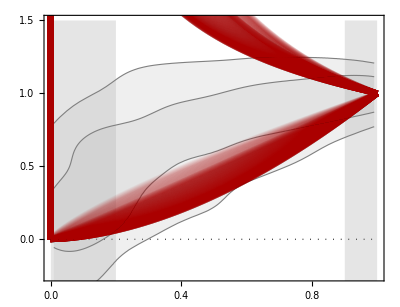

```mathematica
plotDC14GrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        Table[δVDC14[rn,1000,X], {X, Xmin, Xmax, 0.01}], 
        Table[δVDC14[rn,0.001,X], {X, Xmin, Xmax, 0.01}]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Opacity[0.05], Thickness[0.01], Darker[Red]}}
    ]
  }
]
```

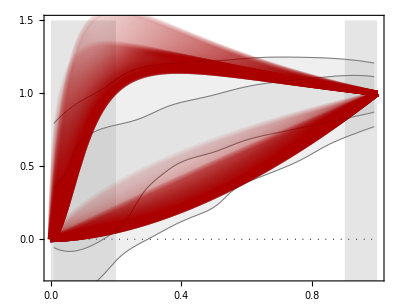

```mathematica
plotDC14GrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        Table[δVDC14[rn,10,X], {X, Xmin, Xmax, 0.01}], 
        Table[δVDC14[rn,0.1,X], {X, Xmin, Xmax, 0.01}]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Opacity[0.05], Thickness[0.01], Darker[Red]}}
    ]
  }
]
```

These definitions below are important if the NFW and Burkert sections were not run

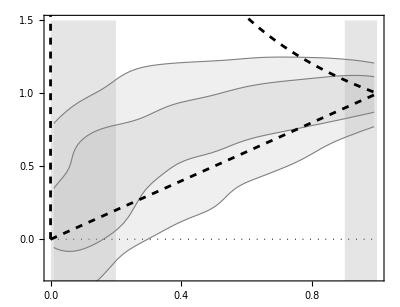
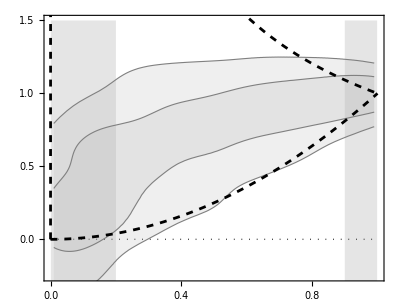
```mathematica
plotNFWGrayRed = -Graphics-;
plotBurkertGrayRed=-Graphics-;
```

```mathematica
σSilverman = 0.082; (*The vertical KDE "error". This value will not be crucial here, since it is constant.*)

Clear[chi2Upper, chi2Lower];
chi2Upper[rsn_?NumberQ, X_, nσ_]:= chi2Upper[rsn, X, nσ] =  NIntegrate[
  (upperBound[nσ][rn] - δVDC14[rn, rsn, X])^2/ σSilverman^2 ,
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision -> 10, 
  PrecisionGoal -> 3, 
  AccuracyGoal -> Infinity, 
  MaxRecursion -> 10
];

chi2Lower[rsn_?NumberQ, X_, nσ_] := chi2Lower[rsn, X, nσ] = NIntegrate[
  (lowerBound[nσ][rn]- δVDC14[rn,rsn, X])^2/ σSilverman^2 , 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision -> 10, 
  PrecisionGoal -> 3, 
  AccuracyGoal -> Infinity, 
  MaxRecursion -> 10
];


(* SPECIFIC DEFINITIONS *)

rnStart = 0.2;
rnEnd = 0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

ClearAll[rsnUpper, rsnLower];
rsnUpper[2] :=  {rsn, X} /. NMinimize[{chi2Upper[rsn, X, 2], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];
rsnUpper[1] :=  {rsn, X} /. NMinimize[{chi2Upper[rsn, X, 1], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];
rsnLower[2] :=  {rsn, X} /. NMinimize[{chi2Lower[rsn, X, 2], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];
rsnLower[1] :=  {rsn, X} /. NMinimize[{chi2Lower[rsn, X, 1], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];

{rsnUpperR[2], rsnUpperR[1], rsnLowerR[2], rsnLowerR[1]} = Parallelize[
  {rsnUpper[2], rsnUpper[1], rsnLower[2], rsnLower[1]}
];

Echo[{rsnUpperR[1], rsnLowerR[1]}, "{rsn, X} 1σ bounds: "];
Echo[{rsnUpperR[2], rsnLowerR[2]}, "{rsn, X} 2σ bounds: "];
```

Performing the optimization.

{rsn, X} 1σ bounds:   {{0.205538,-1.78988},{2.92487,-1.53639}}

{rsn, X} 2σ bounds:   {{0.139313,-3.88306},{50.,-2.66053}}

```mathematica
σSilverman = 0.082; (*The vertical KDE "error". This value will not be crucial here, since it is constant.*)

Clear[chi2Upper, chi2Lower];
chi2Upper[rsn_?NumberQ, X_, nσ_]:= chi2Upper[rsn, X, nσ] =  NIntegrate[
  (upperBound[nσ][rn] - δVDC14[rn, rsn, X])^2/ σSilverman^2 ,
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision -> 10, 
  PrecisionGoal -> 3, 
  AccuracyGoal -> Infinity, 
  MaxRecursion -> 10
];

chi2Lower[rsn_?NumberQ, X_, nσ_] := chi2Lower[rsn, X, nσ] = NIntegrate[
  (lowerBound[nσ][rn]- δVDC14[rn,rsn, X])^2/  σSilverman^2 , 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision -> 10, 
  PrecisionGoal -> 3, 
  AccuracyGoal -> Infinity, 
  MaxRecursion -> 10
];


(* SPECIFIC DEFINITIONS *)

rnStart = 0.2;
rnEnd = 0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

ClearAll[rsnUpper, rsnLower];
rsnUpper[2] :=  {rsn, X} /. NMinimize[{chi2Upper[rsn, X, 2], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];
rsnUpper[1] :=  {rsn, X} /. NMinimize[{chi2Upper[rsn, X, 1], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];
rsnLower[2] :=  {rsn, X} /. NMinimize[{chi2Lower[rsn, X, 2], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];
rsnLower[1] :=  {rsn, X} /. NMinimize[{chi2Lower[rsn, X, 1], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}][[2]];

{rsnUpperR[2], rsnUpperR[1], rsnLowerR[2], rsnLowerR[1]} = Parallelize[
  {rsnUpper[2], rsnUpper[1], rsnLower[2], rsnLower[1]}
];

Echo[{rsnUpperR[1], rsnLowerR[1]}, "{rsn, X} 1σ bounds: "];
Echo[{rsnUpperR[2], rsnLowerR[2]}, "{rsn, X} 2σ bounds: "];
```

Performing the optimization.

{rsn, X} 1σ bounds:   {{0.205538,-1.78988},{2.69658,-1.54568}}

{rsn, X} 2σ bounds:   {{0.139313,-3.88306},{50.,-2.66053}}

Performing the optimization.

{rsn, X} 1σ bounds:   {{0.205538,-1.78988},{2.69658,-1.54568}}

{rsn, X} 2σ bounds:   {{0.139313,-3.88306},{50.,-2.66053}}

```mathematica
NMinimize[{chi2Lower[rsn, X, 1], 50>rsn>0.1, Xmin < X < Xmax}, {rsn, X}]
```

{0.20025,{rsn→2.69658,X→-1.54568}}

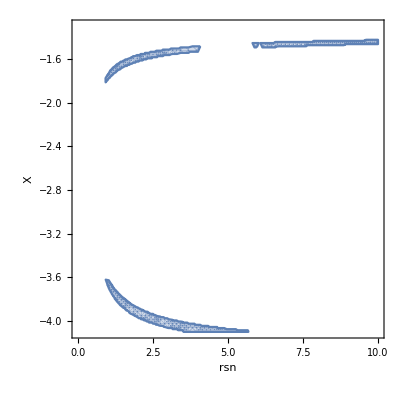

```mathematica
RegionPlot[chi2Lower[rsn, X, 1] < 0.21, {rsn, 0.01, 10}, {X, Xmin, Xmax}, MaxRecursion->4, PlotPoints->20, FrameLabel->Automatic]
```

The above plot shows that there is a strong degeneracy for DC14, at least considering the lower 1σ limiting curve. Hence, the DC14 limiting curves parameter values should be seen as examples that lead to curves that best approximate the observational limits.

plotDC14GlobalBestFit:

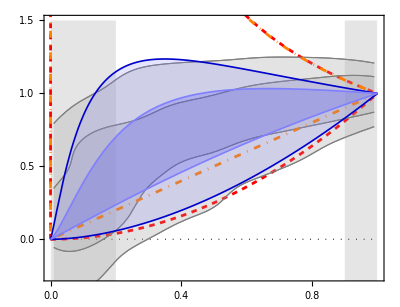

```mathematica
plotDC14GlobalBestFit = Show[
  {
    plotBurkertGrayRed /. {Dashed -> Dashing[.01], Black -> Red},
    plotNFWGrayRed /. {Dashed-> DotDashed, Black -> Orange},
    Plot[
      {
        δVDC14[rn, Sequence@@ rsnUpperR @ 2],
        δVDC14[rn, Sequence@@ rsnUpperR @ 1],
        δVDC14[rn, Sequence@@ rsnLowerR @ 2],
        δVDC14[rn, Sequence@@ rsnLowerR @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotDC14GlobalBestFit:"];
Print@plotDC14GlobalBestFit;

Export["plotDC14GlobalBestFit.pdf", plotDC14GlobalBestFit];
```

The limiting cases above show the burkert (red dashed) and NFW (orange dot-dashed) limits. They coincide in the limit of small r_s or r_c.

The DC14 profile has a clear advantage over the NFW one considering the lower 2σ bound.

## NAV efficiency

```mathematica
efficiencyNAV[δVDC14[#,Sequence@@ rsnLowerR@ 1] &, δVDC14[#, Sequence@@rsnUpperR@ 1] &, 1]
efficiencyNAV[δVDC14[#, Sequence@@rsnLowerR@ 2] &, δVDC14[#, Sequence@@rsnUpperR@ 2] &, 2]
Mean[{%, %%}] (*This is the same of efficiencyNAVtotal*)
```

{0.774499,0.849363,0.0748646}

{0.823292,0.836767,0.0134757}

{0.798895,0.843065,0.0441702}

## Overall Efficiency, Median χ^2 and and χ^2-CDF analysis

Arctan

{0.694453,0.764207,0.0697544}

{0.704059,0.708604,0.00454534}

{0.699256,0.736406,0.0371499}

Median:   8.89515

Total:   7485.48

ArctanHalf

{0.709364,0.78197,0.0726068}

{0.489001,0.489001,0.}

{0.599182,0.635486,0.0363034}

Median:   18.9855

Total:   9867.32

Burkert

{0.738335,0.833853,0.0955181}

{0.86247,0.878446,0.0159759}

{0.800403,0.85615,0.055747}

Median:   8.1357

Total:   8238.22

NFW

{0.771351,0.843344,0.0719928}

{0.633047,0.648073,0.0150251}

{0.732044,0.787845,0.055802}

{0.702199,0.745708,0.0435089}

Median:   19.175

Total:   10058.6

```mathematica
SmoothHistogram[
  {
    Log10@listBurkertChi2, 
    Log10@listArctanChi2, 
    Log10@listNFWChi2, 
    Log10@listArctanHalfChi2
  },
  0.005, 
  "CDF", 
  PlotRange->All, 
  Frame -> True, 
  Axes->False, 
  PlotLegends->Automatic
]
```

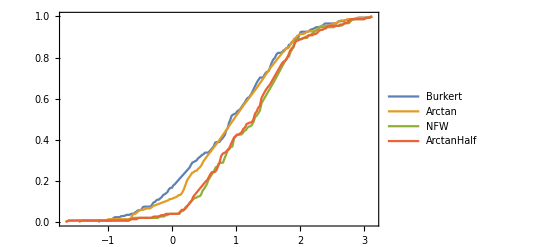

## V. Partially screened gravitational potential: NFW

### V.1 Screened potential limiting cases from NFW

Using rsn for the normalized rs: rs/Rmax and rn for the normalized radius: r/Rmax, the mass and the additional normalized velocity can be them easily computed:

Since

The additional effective mass is given by

γ r^2  m''(r)

Since the mass above will be based on the NFW halo, we call the above MSaddnfw

```mathematica
ρnfw[rn_, rsn_, ρs_] = ρs/(rn/rsn(1+rn/rsn)^2);

Mnfw[rn_, rsn_, ρs_] = 4 π Rmax^3 Integrate[ρnfw[rnprime, rsn, ρs] rnprime^2, {rnprime, 0, rn}, Assumptions-> {rn>0, rsn>0}];

MSaddnfw[rn_, rsn_, ρs_] = rn^2 D[D[Mnfw[rn, rsn, ρs], rn], rn]; (* the effective additional mass*)

MSnfw[rn_, rsn_, ρs_, γ_] = Mnfw[rn, rsn, ρs] + γ MSaddnfw[rn, rsn, ρs]; (*The total effective halo mass*)

VVSnfw[rn_, rsn_, ρs_, γ_] = G/Rmax MSnfw[rn, rsn, ρs, γ]/rn;

δVSnfw[rn_, rsn_, γ_] = FullSimplify[
  VVSnfw[rn, rsn, ρs, γ] / VVSnfw[1, rsn, ρs, γ],
  Assumptions -> {0 < rn < 1, 0 < rsn < 1, 0 < Rmax}
];
```

For rsn → ∞ or rsn → 0, δVSnfw is independent from γ, and hence it has the same result of NFW.

```mathematica
Limit[δVSnfw[rn, rsn,γ] - δVSnfw[rn, rsn,0], rsn -> ∞]
Limit[δVSnfw[rn, rsn,γ] - δVSnfw[rn, rsn,0], rsn -> 0]
```

0

0

But there is an exception: when γ=-1/2 , which is a  singular value at rsn -> ∞

```mathematica
Limit[δVSnfw[rn, rsn,-1/2] - δVSnfw[rn, rsn,0], rsn -> ∞]
Limit[δVSnfw[rn, rsn,-1/2] - δVSnfw[rn, rsn,0], rsn -> 0]
```

(-1+rn) rn

0

```mathematica
δVSnfw[rn, rsn,γ]
```

((1+rsn)^3 (rn ((rn+rsn)^2+rn (rn-rsn) γ)+(rn+rsn)^3 Log[rsn/(rn+rsn)]))/(rn (rn+rsn)^3 (1+rsn (2+rsn-γ)+γ-2 (1+rsn)^3 ArcCoth[1+2 rsn]))

The expression above in general has a singularity that depends on rsn and γ.

The value of γ with a singularity is given by

```mathematica
γsing = γ /. Solve[(1+rsn (2+rsn-γ)+γ-2 (1+rsn)^3 ArcCoth[1+2 rsn]) == 0, γ] // First
```

(-1-2 rsn-rsn^2+2 (1+rsn)^3 ArcCoth[1+2 rsn])/(1-rsn)

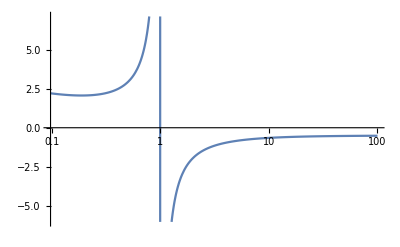

```mathematica
LogLinearPlot[γsing, {rsn, 0, 100}]
```

We intend to find now a range on the values of γ such that no singularity exists, for any rsn value.

```mathematica
FindMinimum[{γsing , 0<rsn<1}, rsn]
Quiet@Maximize[{γsing , rsn>1}, rsn]
```

{2.06866,{rsn→0.188448}}

{-1/2,{rsn→∞}}

For rsn < 1, the values of γ that make the additional contribution to diverge are positive and larger than 2 (larger than 2.069)
For rsn =1, there is no singularity.
For rsn> 1, the values of γ that make the additional contribution to diverse are negative and smaller than - 1/2.

Hence, in the range  -1/2 <  γ < 2 there is no singularity for any rsn value.

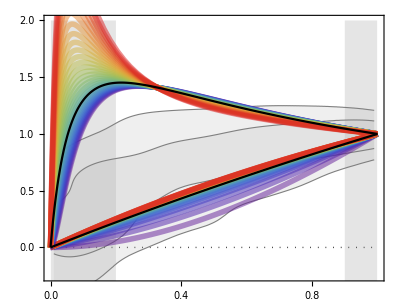

```mathematica
γmin = -0.5;
γmax = 1; (*I could have used γmax = 2, but it gets far away from the observational data*)

nγ = (γmax - γmin)/0.05 + 1;

plotSNFWGrayRed = Show[
  {
    plotBackground[2.0],
    plotSigmaRegionsRAR,
    Plot[
      {
        Evaluate@Table[δVSnfw[rn, 10, X], {X, γmin, γmax, 0.05}], 
        Evaluate@Table[δVSnfw[rn, 0.1, X], {X, γmin, γmax, 0.05}],
        δVSnfw[rn, 0.1, 0],
        δVSnfw[rn, 10, 0]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {Sequence@@Table[{Opacity[0.5], Thickness[0.01], ColorData["Rainbow"][i/nγ]}, {i, nγ}], Sequence@@Table[{Opacity[0.5], Thickness[0.01], ColorData["Rainbow"][i/nγ]}, {i, nγ}], {Black}, {Black}}
    ]
  }
]
```

### V.2. Screened NFW: Highest Density Regions for variable γ

I want to find the values of rsn that best describe the n-sigma regions.

```mathematica
plotNFWGrayRed = -Graphics-;
plotBurkertGrayRed=-Graphics-;
```

```mathematica
σSilverman = 0.082; (*The vertical KDE "error". This value will not be crucial here, since it is constant.*)

Clear[chi2Upper, chi2Lower];
chi2Upper[rsn_?NumberQ, γ_, nσ_]:= chi2Upper[rsn, γ, nσ] =  NIntegrate[
  (upperBound[nσ][rn] - δVSnfw[rn, rsn, γ])^2/ σSilverman^2 ,
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision -> 10, 
  PrecisionGoal -> 3, 
  AccuracyGoal -> Infinity, 
  MaxRecursion -> 10
];

chi2Lower[rsn_?NumberQ, γ_, nσ_] := chi2Lower[rsn, γ, nσ] = NIntegrate[
  (lowerBound[nσ][rn]- δVSnfw[rn,rsn, γ])^2/  σSilverman^2 , 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision -> 10, 
  PrecisionGoal -> 3, 
  AccuracyGoal -> Infinity, 
  MaxRecursion -> 10
];


(* SPECIFIC DEFINITIONS *)

rnStart = 0.2;
rnEnd = 0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

ClearAll[rsnUpper, rsnLower];
rsnUpper[2] :=  {rsn, γ} /. NMinimize[{chi2Upper[rsn, γ, 2], 50>rsn>0.1, γmin < γ < γmax}, {rsn, γ}][[2]];
rsnUpper[1] :=  {rsn, γ} /. NMinimize[{chi2Upper[rsn, γ, 1], 50>rsn>0.1, γmin < γ < γmax}, {rsn, γ}][[2]];
rsnLower[2] :=  {rsn, γ} /. NMinimize[{chi2Lower[rsn, γ, 2], 50>rsn>0.1, γmin < γ < γmax}, {rsn, γ}][[2]];
rsnLower[1] :=  {rsn, γ} /. NMinimize[{chi2Lower[rsn, γ, 1], 50>rsn>0.1, γmin < γ < γmax}, {rsn, γ}][[2]];

{rsnUpperR[2], rsnUpperR[1], rsnLowerR[2], rsnLowerR[1]} = Parallelize[
  {rsnUpper[2], rsnUpper[1], rsnLower[2], rsnLower[1]}
];

Echo[{rsnUpperR[1], rsnLowerR[1]}, "{rsn, γ} 1σ bounds: "];
Echo[{rsnUpperR[2], rsnLowerR[2]}, "{rsn, γ} 2σ bounds: "];
```

Performing the optimization.

{rsn, γ} 1σ bounds:   {{1.31022,1.},{6.46224,0.0888792}}

{rsn, γ} 2σ bounds:   {{0.136188,-0.5},{50.,-0.5}}

plotSnfwGlobalBestFit:

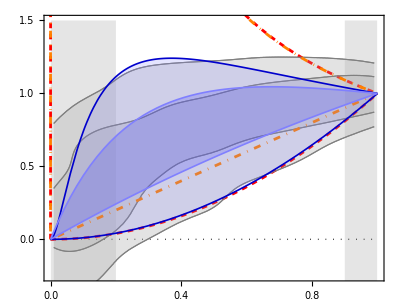

```mathematica
plotSnfwGlobalBestFit = Show[
  {
    plotBurkertGrayRed /. {Dashed -> Dashing[.01], Black -> Red},
    plotNFWGrayRed /. {Dashed -> DotDashed, Black -> Orange},
    Plot[
      {
        δVSnfw[rn, Sequence@@ rsnUpperR @ 2],
        δVSnfw[rn, Sequence@@ rsnUpperR @ 1],
        δVSnfw[rn, Sequence@@ rsnLowerR @ 2],
        δVSnfw[rn, Sequence@@ rsnLowerR @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotSnfwGlobalBestFit:"];
Print@plotSnfwGlobalBestFit;

Export["plotSnfwGlobalBestFit.pdf", plotSnfwGlobalBestFit];
```

### V.3 - Efficiency for variable γ

```mathematica
e1 = efficiencyNAV[δVSnfw[#, Sequence@@(rsnLower@ 1)] &, δVSnfw[#, Sequence@@(rsnUpper@ 1)] &, 1]
```

{0.787995,0.862174,0.0741791}

```mathematica
e2 = efficiencyNAV[δVSnfw[#, Sequence@@(rsnLower@ 2)] &, δVSnfw[#, Sequence@@(rsnUpper@ 2)] &, 2]
```

{0.856881,0.872317,0.015436}

```mathematica
(e1 + e2)/2
```

{0.822438,0.867246,0.0448076}

### V.4. Screened NFW: Highest Density Regions for CONSTANT γ

```mathematica
Clear[rsnγUpper,rsnγLower];
rsnγUpper[n_, γ_] :=  {γ, NMinimize[{chi2Upper[rsn, γ, n], 50>rsn>0.1}, rsn]};
rsnγLower[n_, γ_] :=  {γ, NMinimize[{chi2Lower[rsn, γ, n], 50>rsn>0.1}, rsn]};
```

```mathematica
tab = ParallelTable[{γ, Sum[rsnγUpper[n, γ][[2,1]] + rsnγLower[n, γ][[2,1]], {n,1,2}]}, {γ, -0.5, 1, 0.01}];
```

```mathematica
Sort[tab, #1[[2]]<#2[[2]]&]
```

{{-0.5,2.13253},{-0.49,2.60637},{-0.48,2.93568},{-0.47,3.23133},{-0.46,3.50811},{-0.45,3.77376},{-0.44,4.03018},{-0.43,4.27909},{-0.42,4.52261},{-0.41,4.75938},{-0.4,4.99084},{-0.39,5.21729},{-0.38,5.43885},{-0.37,5.65557},{-0.36,5.86744},{-0.35,6.07435},{-0.34,6.27616},{-0.33,6.47264},{-0.32,6.66353},{-0.31,6.84849},{-0.3,7.02716},{-0.29,7.19908},{-0.28,7.36375},{-0.27,7.52059},{-0.26,7.66896},{-0.25,7.80811},{-0.24,7.93721},{-0.23,8.05533},{-0.22,8.1612},{-0.21,8.25382},{-0.2,8.33197},{-0.19,8.39406},{-0.18,8.43826},{-0.17,8.46966},{-0.16,8.49977},{-0.15,8.5288},{-0.14,8.55703},{-0.13,8.58408},{-0.12,8.6103},{-0.11,8.63578},{-0.1,8.66056},{-0.09,8.68587},{-0.08,8.70949},{-0.07,8.73166},{-0.06,8.7543},{-0.05,8.77653},{-0.04,8.79837},{-0.03,8.81986},{-0.02,8.84104},{1.,8.84752},{0.99,8.85762},{-0.01,8.86194},{0.98,8.8681},{0.97,8.87898},{0.,8.88258},{0.96,8.89028},{0.95,8.90201},{0.01,8.90299},{0.94,8.91418},{0.02,8.92319},{0.93,8.92681},{0.92,8.93992},{0.03,8.94281},{0.91,8.95353},{0.04,8.96304},{0.9,8.96764},{0.05,8.98169},{0.89,8.98227},{0.88,8.99745},{0.06,9.00103},{0.87,9.01318},{0.07,9.02029},{0.86,9.02948},{0.08,9.0395},{0.85,9.04732},{0.09,9.05864},{0.84,9.0648},{0.1,9.07773},{0.83,9.08176},{0.11,9.09676},{0.82,9.10046},{0.12,9.11572},{0.81,9.11976},{0.13,9.13458},{0.8,9.13971},{0.14,9.15337},{0.79,9.16028},{0.15,9.17208},{0.78,9.18148},{0.16,9.19071},{0.77,9.20331},{0.17,9.20924},{0.76,9.22573},{0.18,9.22767},{0.19,9.24707},{0.75,9.24875},{0.2,9.26418},{0.74,9.27233},{0.21,9.28324},{0.73,9.29644},{0.22,9.30014},{0.23,9.3179},{0.72,9.32104},{0.24,9.33549},{0.71,9.34607},{0.25,9.35292},{0.26,9.37018},{0.7,9.37147},{0.27,9.38726},{0.69,9.39729},{0.28,9.40418},{0.29,9.42092},{0.68,9.42318},{0.3,9.4375},{0.67,9.44916},{0.31,9.45392},{0.32,9.47016},{0.66,9.4751},{0.33,9.48624},{0.65,9.50086},{0.34,9.50218},{0.35,9.518},{0.64,9.52625},{0.36,9.53483},{0.37,9.54928},{0.63,9.55111},{0.38,9.56551},{0.62,9.57522},{0.39,9.58058},{0.4,9.59544},{0.61,9.59833},{0.41,9.61006},{0.6,9.62018},{0.42,9.62438},{0.43,9.63833},{0.59,9.64049},{0.44,9.6518},{0.58,9.65898},{0.45,9.66466},{0.57,9.67532},{0.46,9.67672},{0.47,9.68774},{0.56,9.68922},{0.48,9.69745},{0.55,9.70042},{0.49,9.70551},{0.54,9.70868},{0.5,9.71152},{0.53,9.71388},{0.51,9.71513},{0.52,9.71599}}

So the best gamma is γ = - 0.5. Note that this γ value only has a singularity at rsn -> ∞. Lower values of γ have singularity at finite rsn values.

plotSNFWglobalGammaGrayRed:

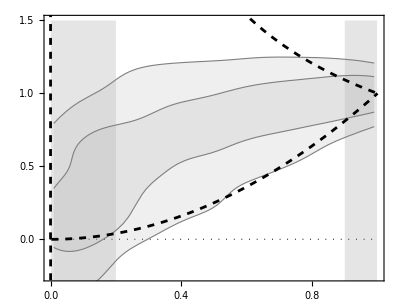

```mathematica
γbest = -0.5;

plotSNFWglobalGammaGrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        δVSnfw[rn, 1000, γbest], 
        δVSnfw[rn, 0.001, γbest]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Thickness[0.005], Black, Dashed}}
    ]
  }
];

Echo["plotSNFWglobalGammaGrayRed:"];
Print@plotSNFWglobalGammaGrayRed;
```

I want to find the values of rsn that best describe the n-sigma regions.

Performing the optimization.

rsn 1σ bounds:   {0.206369,0.986519}

rsn 2σ bounds:   {0.119189,2606.74}

plotNFWGlobalGammaBestFit:

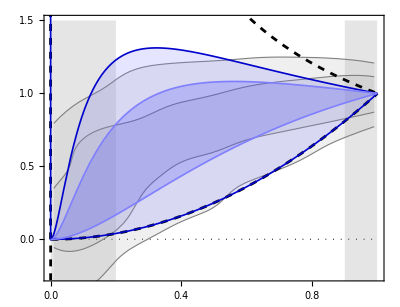

```mathematica
(* SPECIFIC DEFINITIONS *)

rnStart = 0.01;
rnEnd=0.99;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

rsnUpper[2] = rsn /. NMinimize[{chi2Upper[rsn, γbest, 2], rsn > 0}, {rsn, 0, 1}][[2]];
rsnUpper[1] = rsn /. NMinimize[{chi2Upper[rsn, γbest, 1], rsn > 0}, {rsn, 0, 1}][[2]];
rsnLower[2] = rsn /. NMinimize[{chi2Lower[rsn, γbest, 2], rsn > 0}, {rsn, 10, 1000}][[2]];
rsnLower[1] = rsn /. NMinimize[{chi2Lower[rsn, γbest, 1], rsn > 0}, {rsn, 10, 1000}][[2]];

Echo[{rsnUpper[1], rsnLower[1]}, "rsn 1σ bounds: "];
Echo[{rsnUpper[2], rsnLower[2]}, "rsn 2σ bounds: "];

plotNFWGlobalGammaBestFit = Show[
  {
    plotSNFWglobalGammaGrayRed,
    Plot[
      {
        δVSnfw[rn, rsnUpper @ 2, γbest],
        δVSnfw[rn, rsnUpper @ 1, γbest],
        δVSnfw[rn, rsnLower @ 2, γbest],
        δVSnfw[rn, rsnLower @ 1, γbest]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotNFWGlobalGammaBestFit:"];
Print@plotNFWGlobalGammaBestFit;

Export["plotNFWGlobalGammaBestFit.pdf", plotNFWGlobalGammaBestFit];
```

### V.5 - Efficiency for CONSTANT γ

```mathematica
rsnLower@ 1
```

0.986519

```mathematica
Sequence@@(rsnLower@ 1)
```

0.986519

```mathematica
e1 = efficiencyNAV[δVSnfw[#, Sequence@@(rsnLower@ 1), γbest] &, δVSnfw[#, Sequence@@(rsnUpper@ 1), γbest] &, 1]
```

{0.689171,0.886622,0.197451}

```mathematica
e2 = efficiencyNAV[δVSnfw[#, Sequence@@(rsnLower@ 2), γbest] &, δVSnfw[#, Sequence@@(rsnUpper@ 2), γbest] &, 2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.836023,0.887752,0.0517292}

```mathematica
(e1 + e2)/2
```

{0.762597,0.887187,0.12459}

This efficiency is a bit better than the Burkert efficiency!

## TYPE 2 MODELS:

## VII. Palatini

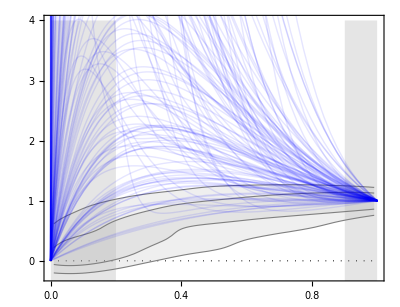

```mathematica
δvP2g[rn_, hn_, fh_, frho_]= (rn ( ⅇ^(-rn/hn)+  frho  fh ⅇ^(- fh rn/hn)))/( ⅇ^(-1/hn)+  frho fh  ⅇ^(- fh /hn));
δv2Palatini[rn_, gal_] := δvP2g[rn, list1hn[[gal]], list1fh[[gal]], list1frho[[gal]]];
Show[plotBackground[4.0],
  plotSigmaRegionsRARNoBulge,
  Plot[Evaluate[δv2Palatini[rn, #] & /@ Range@122], {rn, 0, 1}, 
PlotRange -> All, 
PlotStyle-> Directive[Opacity[0.1],Blue, Thick]]
]
```

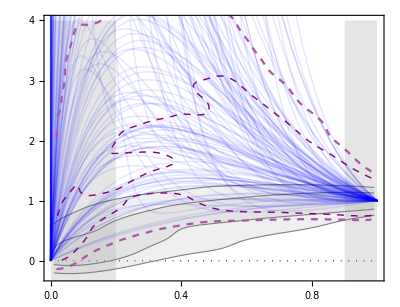

```mathematica
saveThisPlot = False;

Clear @ list2δVVmodel;
list2δVVmodel[gal_] := Table[{rn, δv2Palatini[rn, gal]}, {rn, RandomReal[1, 350]}];
list2δVVmodelAll = Flatten[DeleteCases[list2δVVmodel /@ Range @ 122, {}], 1];

list2δVVmodelAlllimit = Select[list2δVVmodelAll, #[[2]] < 5 &]; (*Data points with δv larger than 5 are not considered, too far. This is just an approximation*)

distPalatini = distributionSilverman[list2δVVmodelAlllimit, 400]; (*Due to the large dispersion of data points, 400 InterpolationPoints are used*)
pdfValuenSigmaPalatini[n_?NumberQ] := FindHDPDFValues[distPalatini, nSigmaProbability[n]];
(*plotBluePalatini = plotBlue[list2δVVmodelAll, list1LimitsSigmaPalatini, {{xmin, xmax - 0.01}, {-0.5, 2.5}}, PlotRange -> {{0, 0.99}, {-0.5, 2.5}}] *)

Clear[plotPalatiniSigma];
plotPalatiniSigma[n_] := plotPalatiniSigma[n] = Block[{pdfValue, contourStyle},
  pdfValue = pdfValuenSigmaPalatini[n];
  Which[
    n == 1, contourStyle = Directive[Purple, Dashed, Thick], 
    n == 2, contourStyle = Directive[Lighter @ Purple, Dashed],
    True, Automatic
  ];
  ContourPlot[
    PDF[distPalatini, {x,y}] == pdfValue, 
    {x, 0, 1}, {y, -1, 5},
    PerformanceGoal -> "Quality", 
    ContourStyle -> contourStyle
  ]
];

plotPalatiniCurves = Plot[
  Evaluate[δv2Palatini[rn, #] & /@ Range@122], 
  {rn, 0, 1}, 
  PlotRange -> All, 
  PlotStyle -> Directive[Opacity[0.1],
  Blue, 
  Thick]
];

plotPalatiniContours = Show[
  {plotPalatiniSigma[1], 
  plotPalatiniSigma[2]}
];
  
Show[
  plotBackground[4.0],
  plotSigmaRegionsRARNoBulge,
  plotPalatiniCurves,
  plotPalatiniContours
]

savePreviousPlot["plotdeltaVPalatini.pdf"]
```

The regions above were found excluding points with δv > 5. The true contour regions are even farther from this case. Without this limit, the dispersion is so large that numerical issues appear.

### NAV efficiency: the second component has numerical issues to be computed.

```mathematica
DistributeDefinitions["NAVbaseCode`"];
DistributeDefinitions["NAVbaseCode`Private`"];

EchoTiming[
{rI[1], rD[1]} = Parallelize[{
  regionIntersection[plotPalatiniSigma[1],1], 
  regionDifference[plotPalatiniSigma[1],1]
  }]
];

efficiencyNAV[1]
```

222.47

-2.50162

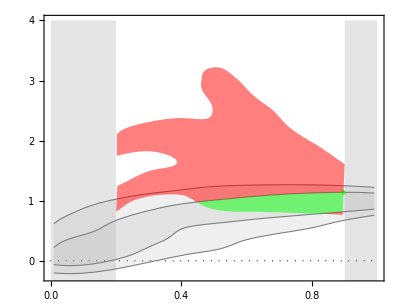

```mathematica
Show[plotBackground[4], plotSigmaRegionsRARNoBulge,rI[1] /. Region[x__] :> Region[Style[x,Opacity[0.5],Green]], rD[1]/. Region[x__] :> Region[Style[x, Opacity[0.5],Red] ]]
```

## VIII. MOND without approximations (153 galaxies, “MondRaw”)

a0 =   1

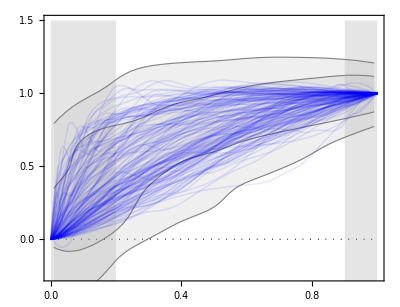

```mathematica
Clear[a0, ΔVVmodel, VVmodel, δVVmodel];

saveThisPlot = False; (*Change this to True to save it*)

v2MondRaw[R_, gal_] := R kpc aBar[R, gal]/(1 - ⅇ^(-√(RealAbs[aBar[R, gal]]/a0)));

Δv2MondRaw[R_, gal_] := v2MondRaw[R, gal] - aBar[R, gal] R kpc ;

δv2MondRaw[rn_, gal_] := If[gdR["Rad", gal]=={}, 
  {}, 
  Δv2MondRaw[rn rmax[gal], gal] / Δv2MondRaw[rmax[gal], gal]
];

Echo[a0 = 1, "a0 = "];
Show[
  plotBackground[1.5],
  plotSigmaRegionsRAR,
  Plot[
    Evaluate[δv2MondRaw[rn, #]& /@ Range@175], {rn,0,1}, 
    PlotStyle-> Directive[Opacity[0.1],Blue, Thick], PlotRange -> All
  ]
]

savePreviousPlot["plotdeltaVmonda01.pdf"];
```

a0 =   1.×10^-15

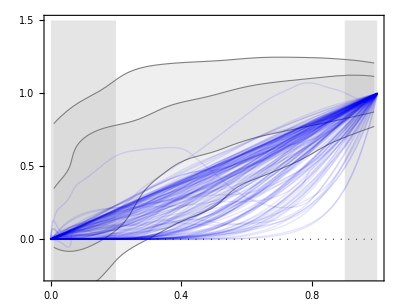

```mathematica
saveThisPlot = False;

Echo[a0 = 1. 10^-15, "a0 = "];
Show[
  plotBackground[1.5],
  plotSigmaRegionsRAR,
  Plot[
    Evaluate[δv2MondRaw[rn, #]& /@ Range@175], {rn,0,1},  
    PlotStyle -> Directive[Opacity[0.1], Blue, Thick], PlotRange -> All
  ]
]

savePreviousPlot["plotdeltaVmonda015.pdf"];
```

The galaxy with a bump above 1 has the number 114. It has an unusual feature: at about rn = 0.8 it has a local minimum in its acceleration. Hence, this oscilation above is not a numerical error, it reflects a property of this galaxy.

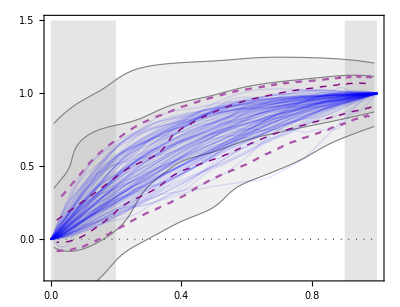

```mathematica
saveThisPlot = False;

a0 = 1.2 10^-13;
Clear @ list2δv2MondRaw;
list2δv2MondRaw[gal_] := If[
  gdR["Rad", gal] == {},
  {},
  Table[{rn, δv2MondRaw[rn, gal]}, {rn, RandomReal[1,70]}]
];
list2δv2MondRawAll = Flatten[DeleteCases[list2δv2MondRaw /@ Range @ 175, {}], 1];

distMondRaw = distributionSilverman @ list2δv2MondRawAll;

pdfValuenSigmaMondRaw[n_?NumberQ] := FindHDPDFValues[distMondRaw, nSigmaProbability[n]];

plotMondRawSigma[n_] := plotMondRawSigma[n] = Block[{pdfValue, contourStyle},
  pdfValue = pdfValuenSigmaMondRaw[n];
  Which[
    n == 1, contourStyle = Directive[Purple, Dashed, Thick], 
    n == 2, contourStyle = Directive[Lighter @ Purple, Dashed],
    True, Automatic
  ];
  ContourPlot[
    PDF[distMondRaw, {x,y}] == pdfValue, 
    {x, 0, 1}, {y, -1, 5},
    PerformanceGoal -> "Quality", 
    ContourStyle -> contourStyle
  ]
];

plotMondRawCurves = Plot[
  Evaluate[δv2MondRaw[rn, #] & /@ Range@122], 
  {rn, 0, 1}, 
  PlotRange -> All, 
  PlotStyle -> Directive[Opacity[0.1],
  Blue, 
  Thick]
];

plotMondRawContours = Show[
  {plotMondRawSigma[1], 
  plotMondRawSigma[2]}
];
  
Show[
  plotBackground[1.5],
  plotSigmaRegionsRAR,
  plotMondRawCurves,
  plotMondRawContours
]

savePreviousPlot["plotdeltaVmondPrincipal.pdf"];
```

### NAV efficiency

```mathematica
DistributeDefinitions["NAVbaseCode`"];
DistributeDefinitions["NAVbaseCode`Private`"];

EchoTiming[
{rI[1], rD[1], rI[2], rD[2]} = Parallelize[{
  regionIntersection[plotMondRawSigma[1],1], 
  regionDifference[plotMondRawSigma[1],1],
  regionIntersection[plotMondRawSigma[2],2],
  regionDifference[plotMondRawSigma[2],2]
  }]
];

efficiencyNAV[1]
efficiencyNAV[2]
efficiencyNAVtotal[]
```

157.94

0.514728

0.544275

0.529501

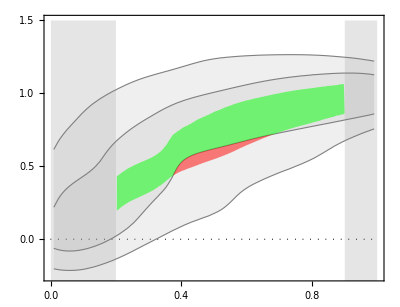

```mathematica
Show[plotBackground[1.5], plotSigmaRegionsRARNoBulge,rI[1] /. Region[x__] :> Region[Style[x,Opacity[0.5],Green]], rD[1]/. Region[x__] :> Region[Style[x, Opacity[0.5],Red] ]]
```

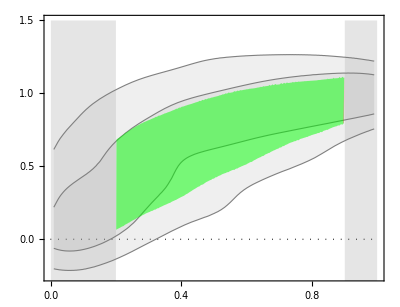

```mathematica
Show[plotBackground[1.5], plotSigmaRegionsRARNoBulge,rI[2] /. Region[x__] :> Region[Style[x,Opacity[0.5], Green]], rD[2]/. Region[x__] :> Region[Style[x, Opacity[0.5], Red] ]]
```

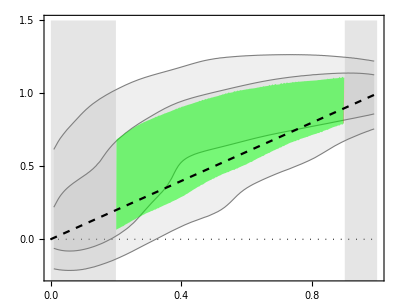

```mathematica
Show[-Graphics-,Show[plotBackground[1.5], Plot[x,{x,0,1}, PlotStyle-> {Dashed, Black}]]]
```

## IX. MOND with exponential approximations (122 galaxies, “MondExp”)

```mathematica
Clear[a0];

a0Max = 1.;
a0Min = 1. 10^-15;
a0Std = 1.2 10^-13;

aBarExp[R_, gal_] :=  vBarExp[R, gal]^2/(R kpc);
v2MondExp[R_, gal_] := R kpc aBarExp[R, gal]/(1 - ⅇ^(-√(aBarExp[R, gal]/a0)));
Δv2MondExp[R_, gal_] := v2MondExp[R, gal] - vBarExp[R, gal]^2;

δv2MondExpAux[rn_, gal_] := Δv2MondExp[rn rmax122[gal], gal]/Δv2MondExp[rmax122[gal], gal];

Clear[tableδv2MondExp, a0];
tableδv2MondExp[a0_] = ParallelTable[{rn, δv2MondExpAux[rn, gal]}, {gal, 122}, {rn, 0.01, 1, 0.01} ];
```

a0 =   1.

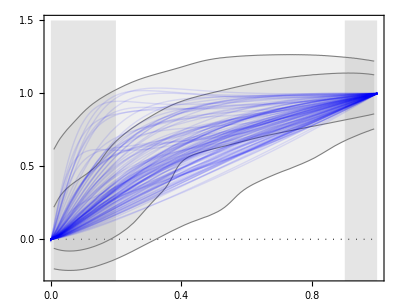

```mathematica
saveThisPlot = False; (*Change this to True to save it*)

Clear[δv2MondExp];

(δv2MondExpMax[rn_, #] = Interpolation[tableδv2MondExp[a0Max][[#]], Method -> "Spline"][rn])& /@ Range@122;
Echo[a0Max, "a0 = "];
Show[
  plotBackground[1.5],
  plotSigmaRegionsRARNoBulge,
  Plot[
    Evaluate[δv2MondExpMax[rn, #]& /@ Range@122], {rn,0,1}, 
    PlotStyle-> Directive[Opacity[0.1],Blue, Thick], PlotRange -> All
  ]
]

savePreviousPlot["plotdeltaVmondExpa01.pdf"];
```

a0 =   1.×10^-15

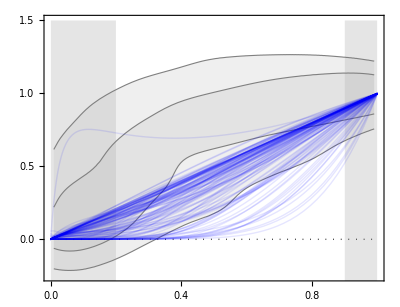

```mathematica
saveThisPlot = False;

(δv2MondExpMin[rn_, #] = Interpolation[tableδv2MondExp[a0Min][[#]], Method -> "Spline"][rn])& /@ Range@122;
Echo[a0Min, "a0 = "];
Show[
  plotBackground[1.5],
  plotSigmaRegionsRARNoBulge,
  Plot[
    Evaluate[δv2MondExpMin[rn, #]& /@ Range@122], {rn,0,1}, 
    PlotStyle-> Directive[Opacity[0.1],Blue, Thick], PlotRange -> All
  ]
]

savePreviousPlot["plotdeltaVmondExp015.pdf"];
```

a0 =   1.2×10^-13

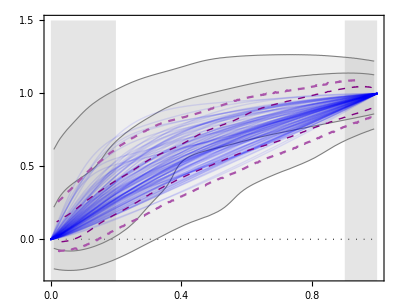

```mathematica
saveThisPlot = False;

(δv2MondExp[rn_, #] = Interpolation[tableδv2MondExp[a0Std][[#]], Method -> "Spline"][rn]) & /@ Range @ 122;

list2δv2MondExp[gal_] := Table[{rn, δv2MondExp[rn, gal]}, {rn, RandomReal[1, 70]}];

list2δv2MondExpAll = Flatten[list2δv2MondExp /@ Range @ 122, 1];

distMondExp = distributionSilverman @ list2δv2MondExpAll;

pdfValuenSigmaMondExp[n_?NumberQ] := FindHDPDFValues[distMondExp, nSigmaProbability[n]];

plotMondExpSigma[n_] := plotMondExpSigma[n] = Block[{pdfValue, contourStyle},
  pdfValue = pdfValuenSigmaMondExp[n];
  Which[
    n == 1, contourStyle = Directive[Purple, Dashed, Thick], 
    n == 2, contourStyle = Directive[Lighter @ Purple, Dashed],
    True, Automatic
  ];
  ContourPlot[
    PDF[distMondExp, {x,y}] == pdfValue, 
    {x, 0, 1}, {y, -1, 5},
    PerformanceGoal -> "Quality", 
    ContourStyle -> contourStyle
  ]
];

plotMondExpCurves = Plot[
  Evaluate[δv2MondExp[rn, #] & /@ Range @ 122], 
  {rn, 0, 1}, 
  PlotStyle -> Directive[Opacity[0.1], Blue, Thick], 
  PlotRange -> All
];

plotMondExpContours = Show[{plotMondExpSigma[1], plotMondExpSigma[2]}];

Echo[a0Std, "a0 = "];
Show[
  plotBackground[1.5],
  plotSigmaRegionsRARNoBulge,
  plotMondExpCurves,
  plotMondExpContours
]

savePreviousPlot["plotdeltaVmondExpPrincipal.pdf"];
```

### NAV efficiency

```mathematica
DistributeDefinitions["NAVbaseCode`"];
DistributeDefinitions["NAVbaseCode`Private`"];

EchoTiming[
{rI[1], rD[1], rI[2], rD[2]} = Parallelize[{
  regionIntersection[plotMondExpSigma[1],1], 
  regionDifference[plotMondExpSigma[1],1],
  regionIntersection[plotMondExpSigma[2],2],
  regionDifference[plotMondExpSigma[2],2]
  }]
];

efficiencyNAV[1]
efficiencyNAV[2]
efficiencyNAVtotal[]
```

121.61

0.330612

0.501306

0.415959

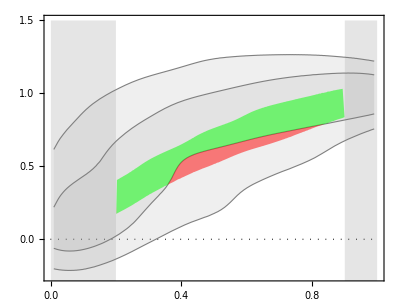

```mathematica
Show[plotBackground[1.5], plotSigmaRegionsRARNoBulge,rI[1] /. Region[x__] :> Region[Style[x,Opacity[0.5],Green]], rD[1]/. Region[x__] :> Region[Style[x, Opacity[0.5],Red] ]]
```

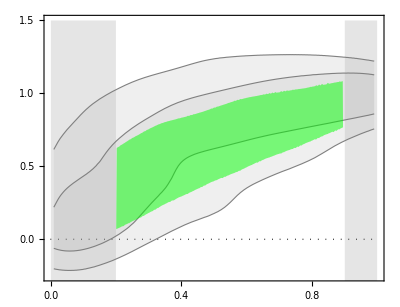

```mathematica
Show[plotBackground[1.5], plotSigmaRegionsRARNoBulge,rI[2] /. Region[x__] :> Region[Style[x,Opacity[0.5], Green]], rD[2]/. Region[x__] :> Region[Style[x, Opacity[0.5], Red] ]]
```

## IX. RGGR

```mathematica
Clear[phiExpDisk, phiExpGal, phiExpGal, ΔVVRGGR, δVVRGGR]


Δv2Rggr[R_, gal_] := - v2Infty vBarExp[R, gal]^2 / phiBarExp[R, gal];

δv2RggrAux[rn_, gal_Integer] := Δv2Rggr[rn rmax122[gal], gal] / Δv2Rggr[rmax122[gal], gal];

tableδv2Rggr = ParallelTable[{rn, δv2RggrAux[rn, gal]}, {gal, 122}, {rn, 0.01, 1, 0.01} ];

(δv2Rggr[rn_, #] = Interpolation[tableδv2Rggr[[#]], Method -> "Spline"][rn]) & /@ Range @ 122;

(*
l1δVVRGGR[rni_] = Block[
  {l2δVVRGGRAux},
  l2δVVRGGRAux[gali_] := Prepend[
    Table[{rni, δVVRGGRAux[rni, gali]}, {rni, 0.05, 1, 0.05}], 
    {0,0}
  ];
  Table[
    Interpolation[l2δVVRGGRAux[gali]][rni], 
  {gali, nG}
  ]
];

δVVRGGR[rn_, gal_] :=  l1δVVRGGR[rn][[gal]]*)
```

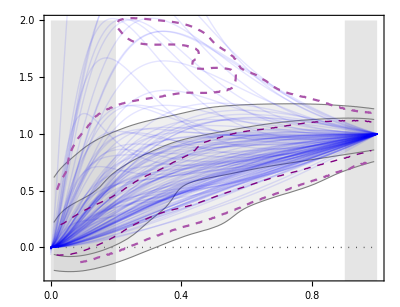

```mathematica
saveThisPlot = False; 

list2δv2Rggr[gal_] := Table[{rn, δv2Rggr[rn, gal]}, {rn, RandomReal[1, 70]}]; (*Picks random points along each model curve*)

list2δv2RggrAll = Flatten[list2δv2Rggr /@ Range @ 122, 1];

distRggr = distributionSilverman @ list2δv2RggrAll;

pdfValuenSigmaRggr[n_?NumberQ] := FindHDPDFValues[distRggr, nSigmaProbability[n]];

plotRggrSigma[n_] := plotRggrSigma[n] = Block[{pdfValue, contourStyle},
  pdfValue = pdfValuenSigmaRggr[n];
  Which[
    n == 1, contourStyle = Directive[Purple, Dashed, Thick], 
    n == 2, contourStyle = Directive[Lighter @ Purple, Dashed],
    True, Automatic
  ];
  ContourPlot[
    PDF[distRggr, {x,y}] == pdfValue, 
    {x, 0, 1}, {y, -1, 5},
    PerformanceGoal -> "Quality", 
    ContourStyle -> contourStyle
  ]
];

plotRggrCurves = Plot[
  Evaluate[δv2Rggr[rn, #] & /@ Range @ 122], 
  {rn, 0, 1}, 
  PlotStyle -> Directive[Opacity[0.1], Blue, Thick], 
  PlotRange -> All
];

plotRggrContours = Show[{plotRggrSigma[1], plotRggrSigma[2]}];

Show[
  plotBackground[2],
  plotSigmaRegionsRARNoBulge,
  plotRggrCurves,
  plotRggrContours
]

savePreviousPlot["plotdeltaVRGGR.pdf"];
```

### NAV efficiency

```mathematica
DistributeDefinitions["NAVbaseCode`"];
DistributeDefinitions["NAVbaseCode`Private`"];

EchoTiming[
{rI[1], rD[1], rI[2], rD[2]} = Parallelize[{
  regionIntersection[plotRggrSigma[1],1], 
  regionDifference[plotRggrSigma[1],1],
  regionIntersection[plotRggrSigma[2],2],
  regionDifference[plotRggrSigma[2],2]
  }]
];

efficiencyNAV[1]
efficiencyNAV[2]
efficiencyNAVtotal[]
```

163.223

0.550499

0.66011

0.605304

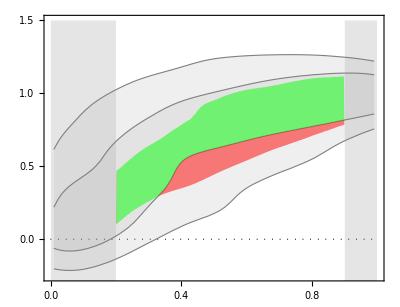

```mathematica
Show[plotBackground[1.5], plotSigmaRegionsRARNoBulge,rI[1] /. Region[x__] :> Region[Style[x,Opacity[0.5],Green]], rD[1]/. Region[x__] :> Region[Style[x, Opacity[0.5],Red] ]]
```

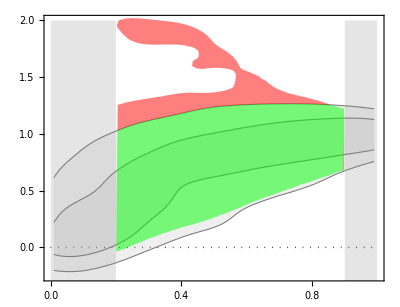

```mathematica
Show[plotBackground[2], plotSigmaRegionsRARNoBulge,rI[2] /. Region[x__] :> Region[Style[x,Opacity[0.5], Green]], rD[2]/. Region[x__] :> Region[Style[x, Opacity[0.5], Red] ]]
```

## X. Moffat’s MOG

A variation to be explored latter: stellar mass from L, instead of the dynamical approximation.

From Green & Moffat, PDU 2019:

```mathematica
Clear[α, μ, μMOG, μMOGinfty, fgas, ΔD0, μMOGstd, μMOGinfty];

D0std = 6.25 10^3; (*std = Standard value*)

Off[NIntegrate::precw];
diffAbs[r_, rprime_, θ_] = Sqrt[r^2 + rprime^2 - 2 r rprime Cos[θ]];

Δv2MOG[r_, α_, μ_, gal_, fgas_] :=  kpc^2 G0 α r NIntegrate[
  sigmaBarExpf[r, gal, fgas]/diffAbs[r, rprime, θ]^2(1 - Exp[- μ diffAbs[r, rprime, θ]] ( 1 + μ diffAbs[r, rprime, θ])) rprime, 
  {θ, -π, π}, {rprime, 0, 1}, 
  Exclusions -> "Singularities", 
  WorkingPrecision -> 30, 
  PrecisionGoal -> 5, 
  AccuracyGoal -> Infinity
];

δv2MOG[rn_, μ_, gal_, fgas_:1] := Δv2MOG[rn rmax122[gal], 1, μ, gal, fgas]/ Δv2MOG[rmax122[gal], 1, μ, gal, fgas]; (*α was used here to be 1, δv2MOG is independ from α*)
μMOG[gal_] := (D0std ΔD0)/(√massExpBar[gal]);
μMOG[gal_, rStarEnd_, rGasEnd_, fgas_] := (D0std ΔD0)/(√massExpBar[gal, rStarEnd, rGasEnd, fgas]);
μMOGstd[gal_] := μMOG[gal, 4.5 hExpStar[gal], rmax122[gal], fgas];
μMOGinfty[gal_] := (D0std ΔD0)/(√massExpInftyBar[gal]);

Clear[tableδv2MOG];
tableδv2MOG[μ_, gal_] := Table[{rn, δv2MOG[rn, μ, gal, fgas]}, {rn, 0.01, 1, 0.0198} ]; (*0.198 for 50 steps per galaxy*)
tableδv2MOG[gal_] := Table[{rn, δv2MOG[rn, μMOG[gal], gal, fgas]}, {rn, 0.01, 1, 0.0198} ];
tableδv2MOGinfty[gal_] := Table[{rn, δv2MOG[rn, μMOGinfty[gal], gal, fgas]}, {rn, 0.01, 1, 0.0198} ];
tableδv2MOGstd[gal_] := Table[{rn, δv2MOG[rn, μMOGstd[gal], gal, fgas]}, {rn, 0.01, 1, 0.0198} ];
```

For the small μ limit, Δv2MOG goes to zero ∝α μ^2. δv2MOG does not go to zero.

Considering the small M or μ limit, Δv2MOG becomes linear on μ^2, as shown below. Consequently, δv2MOG is independent on μ in this limit.

```mathematica
Series[(1 - Exp[- μ diffAbs[r, rprime, θ]] ( 1 + μ diffAbs[r, rprime, θ])), {μ, 0, 2}]
```

1/2 diffAbs[r,rprime,θ]^2 μ^2+O[μ]^3

The following quantities (1/μMOG-type) have dimension of length.

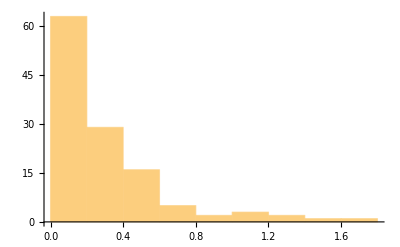
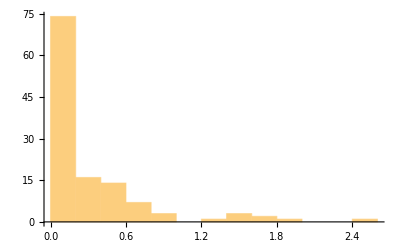
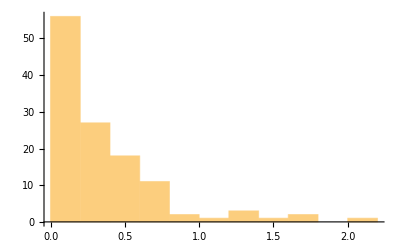

```mathematica
Row@{Histogram[1/μMOG /@ Range @ 122],
Histogram[1/ μMOGinfty /@ Range @ 122],
Histogram[1/ μMOGstd /@ Range @ 122]}
```

The following quantities (hExpStar μMOG) are dimensionless.

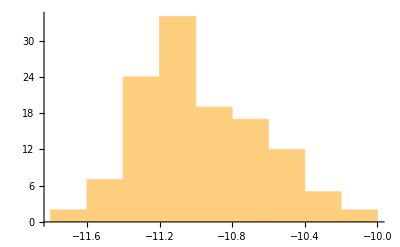
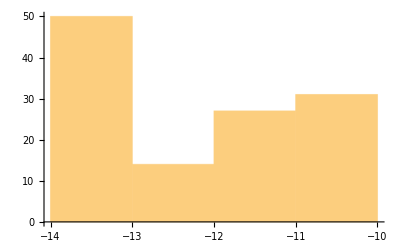
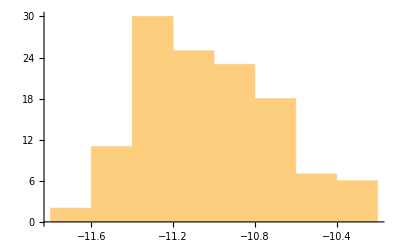

```mathematica
Row@{Histogram[Log10[hExpStar[#] μMOG[#] & /@ Range @ 122]]
Histogram[Log10[hExpStar[#] μMOGinfty[#] & /@ Range @ 122]],
Histogram[Log10[hExpStar[#] μMOGstd[#] & /@ Range @ 122]]}
```

## D0 → 0, fgas = 1.5 -- Seems to be the best combination for MOG

```mathematica
ΔD0 = 10^-10;
fgas = 1.5;

CloseKernels[];
LaunchKernels[];
DistributeDefinitions["NAVbaseCode`"];
DistributeDefinitions["NAVbaseCode`Private`"];
ParallelEvaluate[Off[NIntegrate::precw ]];
EchoTiming[
  tableδv2MOGstdResults =  ParallelTable[tableδv2MOGstd[gal], {gal, 122}];
]
```

63.7771

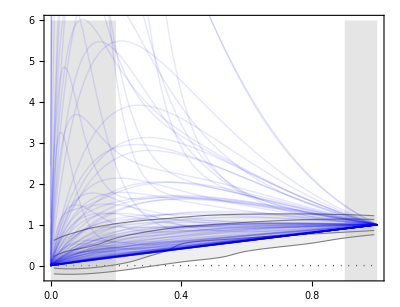

```mathematica
(δv2MOGstd[rn_, #] = Interpolation[tableδv2MOGstdResults[[#]], Method -> "Spline"][rn])& /@ Range@122;

Show[
  plotBackground[6],
  plotSigmaRegionsRARNoBulge,
  Plot[
    Evaluate[δv2MOGstd[rn, #]& /@ Range@122], {rn,0,1}, 
    PlotStyle-> Directive[Opacity[0.1],Blue, Thick], 
PlotRange -> All
  ],
Background->White
]
```

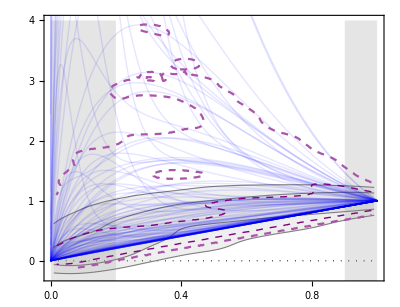

```mathematica
Clear[plotMOGSigma];

list2δv2MOG[gal_] := Table[{rn, δv2MOGstd[rn, gal]}, {rn, RandomReal[1, 200]}]; (*Picks random points along each model curve*)

list2δv2MOGAll = Select[
  Flatten[list2δv2MOG /@ Range @ 122, 1], 
  #[[2]] < 5 &
]; (*Data points with δv2 larger than 5 are not considered, too far. This is just an approximation*)

distMOG = distributionSilverman[list2δv2MOGAll, 400]; (*Due to the large dispersion of data points, 400 InterpolationPoints are used*)

pdfValuenSigmaMOG[n_?NumberQ] := FindHDPDFValues[distMOG, nSigmaProbability[n]];

plotMOGSigma[n_] := plotMOGSigma[n] = Block[{pdfValue, contourStyle},
  pdfValue = pdfValuenSigmaMOG[n];
  Which[
    n == 1, contourStyle = Directive[Purple, Dashed, Thick], 
    n == 2, contourStyle = Directive[Lighter @ Purple, Dashed],
    True, Automatic
  ];
  ContourPlot[
    PDF[distMOG, {x,y}] == pdfValue, 
    {x, 0, 1}, {y, -1, 5},
    PerformanceGoal -> "Quality", 
    ContourStyle -> contourStyle
  ]
];

plotMOGCurves = Plot[
  Evaluate[δv2MOGstd[rn, #] & /@ Range @ 122], 
  {rn, 0, 1}, 
  PlotStyle -> Directive[Opacity[0.1], Blue, Thick], 
  PlotRange -> All
];

plotMOGContours = Show[{plotMOGSigma[1], plotMOGSigma[2]}];

Show[
  plotBackground[4],
  plotSigmaRegionsRARNoBulge,
  plotMOGCurves,
  plotMOGContours,
  Background-> White
]
```

### NAV efficiency: the second component has numerical issues to be computed.

```mathematica
(*DistributeDefinitions["NAVbaseCode`"];
DistributeDefinitions["NAVbaseCode`Private`"];*)

EchoTiming[
{rI[1], rD[1]} = Parallelize[{
  regionIntersection[plotMOGSigma[1],1], 
  regionDifference[plotMOGSigma[1],1]
  }]
];

efficiencyNAV[1]
```

103.094

0.340016

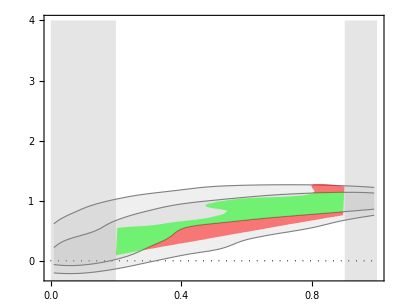

```mathematica
Show[plotBackground[4], plotSigmaRegionsRARNoBulge,rI[1] /. Region[x__] :> Region[Style[x,Opacity[0.5],Green]], rD[1]/. Region[x__] :> Region[Style[x, Opacity[0.5],Red] ]]
```

## D0 standard , fgas = 1.15

```mathematica
ΔD0 = 1;
fgas = 1.15;

CloseKernels[];
LaunchKernels[];
DistributeDefinitions["NAVbaseCode`"];
DistributeDefinitions["NAVbaseCode`Private`"];
ParallelEvaluate[Off[NIntegrate::precw ]];
EchoTiming[
tableδv2MOGstdResults =  ParallelTable[tableδv2MOGstd[gal], {gal, 122}]; ]
```

64.2984

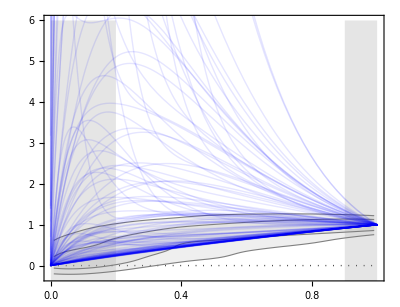

```mathematica
(δv2MOGstd[rn_, #] = Interpolation[tableδv2MOGstdResults[[#]], Method -> "Spline"][rn])& /@ Range@122;

Show[
  plotBackground[6],
  plotSigmaRegionsRARNoBulge,
  Plot[
    Evaluate[δv2MOGstd[rn, #]& /@ Range@122], {rn,0,1}, 
    PlotStyle-> Directive[Opacity[0.1],Blue, Thick], 
PlotRange -> All
  ],
Background->White
]
```

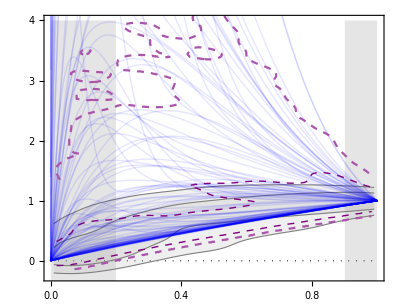

```mathematica
Clear[plotMOGSigma];

list2δv2MOG[gal_] := Table[{rn, δv2MOGstd[rn, gal]}, {rn, RandomReal[1, 200]}]; (*Picks random points along each model curve*)

list2δv2MOGAll = Select[
  Flatten[list2δv2MOG /@ Range @ 122, 1], 
  #[[2]] < 5 &
]; (*Data points with δv2 larger than 5 are not considered, too far. This is just an approximation*)

distMOG = distributionSilverman[list2δv2MOGAll, 400]; (*Due to the large dispersion of data points, 400 InterpolationPoints are used*)

pdfValuenSigmaMOG[n_?NumberQ] := FindHDPDFValues[distMOG, nSigmaProbability[n]];

plotMOGSigma[n_] := plotMOGSigma[n] = Block[{pdfValue, contourStyle},
  pdfValue = pdfValuenSigmaMOG[n];
  Which[
    n == 1, contourStyle = Directive[Purple, Dashed, Thick], 
    n == 2, contourStyle = Directive[Lighter @ Purple, Dashed],
    True, Automatic
  ];
  ContourPlot[
    PDF[distMOG, {x,y}] == pdfValue, 
    {x, 0, 1}, {y, -1, 5},
    PerformanceGoal -> "Quality", 
    ContourStyle -> contourStyle
  ]
];

plotMOGCurves = Plot[
  Evaluate[δv2MOGstd[rn, #] & /@ Range @ 122], 
  {rn, 0, 1}, 
  PlotStyle -> Directive[Opacity[0.1], Blue, Thick], 
  PlotRange -> All
];

plotMOGContours = Show[{plotMOGSigma[1], plotMOGSigma[2]}];

Show[
  plotBackground[4],
  plotSigmaRegionsRARNoBulge,
  plotMOGCurves,
  plotMOGContours,
  Background-> White
]
```

### NAV efficiency: the second component has numerical issues to be computed.

```mathematica
(*DistributeDefinitions["NAVbaseCode`"];
DistributeDefinitions["NAVbaseCode`Private`"];*)

EchoTiming[
{rI[1], rD[1]} = Parallelize[{
  regionIntersection[plotMOGSigma[1],1], 
  regionDifference[plotMOGSigma[1],1]
  }]
];

efficiencyNAV[1]
```

117.214

0.16787

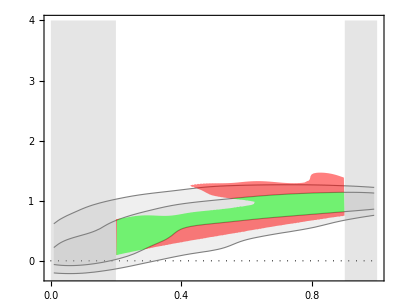

```mathematica
Show[plotBackground[4], plotSigmaRegionsRARNoBulge,rI[1] /. Region[x__] :> Region[Style[x,Opacity[0.5],Green]], rD[1]/. Region[x__] :> Region[Style[x, Opacity[0.5],Red] ]]
```